```mathematica
(*NS CHECK WITH ZUREK MACDERMOTT*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*10^3(*in GeV/m^3*)(*Due to Overdensity*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
(*mphi=10;*)
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
(*asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;*)
```

```mathematica
(*a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));*)
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
ttherm[mx_?NumericQ,sigma_?NumericQ,T_]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*sigma*kb*T);
```

```mathematica
auni[100,sigmasat]
```

7.18413×10^26

```mathematica
agen[100,sigmasat,0.1]
```

7.15855×10^26

```mathematica
tage=10^10*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27);
NxBEC[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*2.612*((mx*T*8.62*10^-14)/(2*π))^1.5*(5.62*10^15)^3;
Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
NchFermion[mx_?NumericQ]:=Mpl^3/mx^3;
```

```mathematica
FindRoot[10^x*Max[Nself[10^x,10^5],NchBoson[10^x]]==5.03086*10^36,{x,0}]//Quiet(*Without BEC*)
```

{x→6.65167}

```mathematica
FindRoot[10^x*Max[NchBoson[10^x]]==5.03806*10^36,{x,0}]//Quiet(*With BEC*)
```

{x→1.27512}

```mathematica
FindRoot[10^x*Max[Nself[10^x,10^5],NchFermion[10^x]]==5.03806*10^36,{x,0}]//Quiet
```

{x→10.279}

```mathematica
10^1.27512
```

18.8417

```mathematica
10^6.65167
```

4.48405×10^6

```mathematica
10^10.279
```

1.90108×10^10

```mathematica
ttherm[1,2.1*10^-49,10^5]/(365*86400)
```

0.000037912

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data1=Import["xenon.dat","Table"];
data2=Import["neutrino_floor.dat","Table"];
data3=Import["darkside50.dat","Table"];
data4=Import["lux.dat","Table"];
```

```mathematica
(*myticks={{{{-44,"10^-40"},{-48,"10^-44"},{-52,"10^-48"},{-56,"10^-52"},{-60,"10^-56"},{-64,"10^-60"}},None},{{{-2,"10^-2"},{-1,"10^-1"},{0,"1"},{1,"10"},{2,"10^2"},{3,"10^3"},{4,"10^4"},{5,"10^5"},{6,"10^6"},{7,"10^7"},{8,"10^8"},{9,"10^9"},{10,"10^10"},{11,"10^11"},{12,"10^12"}},None}};*)
```

```mathematica
(*ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}],Table[{Log10[data2[[i,1]]],-data2[[i,2]]-4},{i,Length[data2]}],Table[{Log10[data3[[i,1]]],-data3[[i,2]]-4},{i,Length[data3]}],Table[{Log10[data4[[i,1]]],-data4[[i,2]]-4},{i,Length[data4]}]},PlotRange->{{0,12},{-44,-64}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2]*)
```

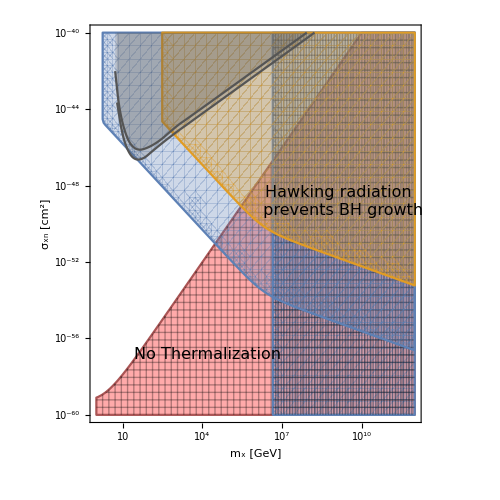

```mathematica
Show[RegionPlot[{ttherm[10^x,10^y,10^5]≥  tage},{x,0,12},{y,-44,-64},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Pink],PlotStyle->Lighter[Pink],Mesh->50,FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{10^x*Nself[10^x,10^5]≤ 5.03086*10^36},{x,0,12},{y,-44,-64},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],Mesh->50,FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{totcapuni[10^x,10^y]≥ Nself[10^x,10^5],0.4/10^3*totcapuni[10^x,10^y]≥ Nself[10^x,10^5]},{x,0,12},{y,-44,-64},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}],Table[{Log10[data4[[i,1]]],-data4[[i,2]]-4},{i,Length[data4]}]},PlotRange->{{0,3},{-44,-64}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{4.2,-60.83}],0 Degree]],Graphics[Rotate[Text[Style["Hawking radiation \n prevents BH growth",Darker[Black],FontSize->16],{9.2,-52.83}],0 Degree]]]//Quiet
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["boson.pdf",-Graphics-];
```

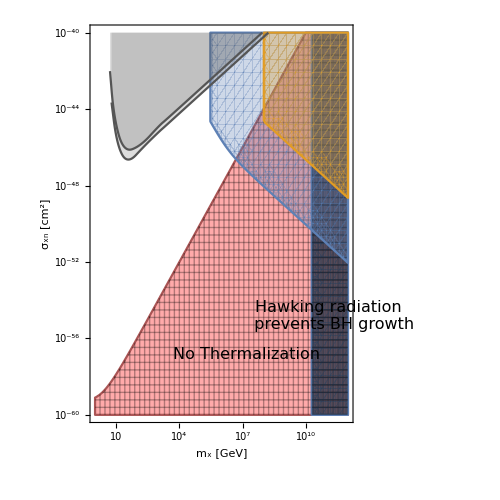

```mathematica
Show[RegionPlot[{ttherm[10^x,10^y,10^5]≥  tage},{x,0,12},{y,-44,-64},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Pink],PlotStyle->Lighter[Pink],Mesh->50,FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{10^x*Max[Nself[10^x,10^5],NchFermion[10^x]]≤ 5.03086*10^36},{x,0,12},{y,-44,-64},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],Mesh->50,FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{totcapuni[10^x,10^y]≥ Max[Nself[10^x,10^5],NchFermion[10^x]],0.4/10^3*totcapuni[10^x,10^y]≥ Max[Nself[10^x,10^5],NchFermion[10^x]]},{x,0,12},{y,-44,-64},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}],Table[{Log10[data4[[i,1]]],-data4[[i,2]]-4},{i,Length[data4]}]},PlotRange->{{0,3},{-44,-64}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{7.2,-60.83}],0 Degree]],Graphics[Rotate[Text[Style["Hawking radiation \n prevents BH growth",Darker[Black],FontSize->16],{11.2,-58.83}],90 Degree]]]//Quiet
```

```mathematica
Export["fermion.pdf",-Graphics-];
```

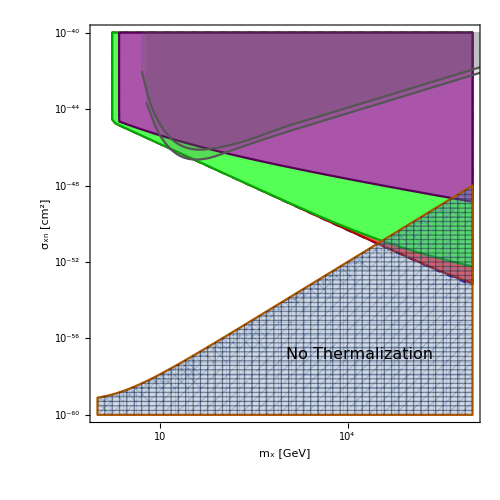

```mathematica
Show[RegionPlot[{totcapuni[10^x,10^y]≥ Nself[10^x,10^5]},{x,0,6},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{totcapgen[10^x,10^y,1]≥ Nself[10^x,10^5]},{x,-2,6},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,PlotStyle->Lighter[Red],BoundaryStyle->{Darker[Red]},ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.1]≥ Nself[10^x,10^5]},{x,-2,6},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->Lighter[Green],BoundaryStyle->{Darker[Green]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.001]≥ Nself[10^x,10^5]},{x,-2,6},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,PlotStyle->Lighter[Purple],BoundaryStyle->{Darker[Purple]},ImageSize->500,FrameTicks->myticks],
RegionPlot[{ttherm[10^x,10^y,10^5]≥   tage},{x,0,6},{y,-44,-64},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Orange],Mesh->50,FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}],Table[{Log10[data4[[i,1]]],-data4[[i,2]]-4},{i,Length[data4]}]},PlotRange->{{0,3},{-44,-64}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{4.2,-60.83}],0 Degree]]]//Quiet
```

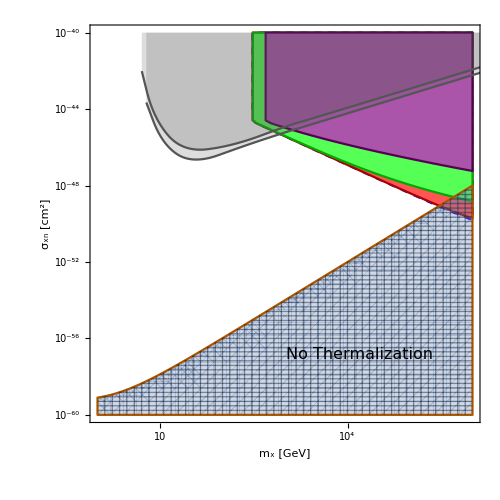

```mathematica
Show[RegionPlot[{0.4/10^3*totcapuni[10^x,10^y]≥ Nself[10^x,10^5]},{x,0,6},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{0.4/10^3*totcapgen[10^x,10^y,1]≥ Nself[10^x,10^5]},{x,-2,6},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,PlotStyle->Lighter[Red],BoundaryStyle->{Darker[Red]},ImageSize->500,FrameTicks->myticks],
RegionPlot[{0.4/10^3*totcapgen[10^x,10^y,0.1]≥ Nself[10^x,10^5]},{x,-2,6},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->Lighter[Green],BoundaryStyle->{Darker[Green]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{0.4/10^3*totcapgen[10^x,10^y,0.01]≥ Nself[10^x,10^5]},{x,-2,6},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,PlotStyle->Lighter[Purple],BoundaryStyle->{Darker[Purple]},ImageSize->500,FrameTicks->myticks],
RegionPlot[{ttherm[10^x,10^y,10^5]≥   tage},{x,0,6},{y,-44,-64},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Orange],Mesh->50,FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}],Table[{Log10[data4[[i,1]]],-data4[[i,2]]-4},{i,Length[data4]}]},PlotRange->{{0,3},{-44,-64}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{4.2,-60.83}],0 Degree]]]//Quiet
```

```mathematica
(*with BEC*)
```

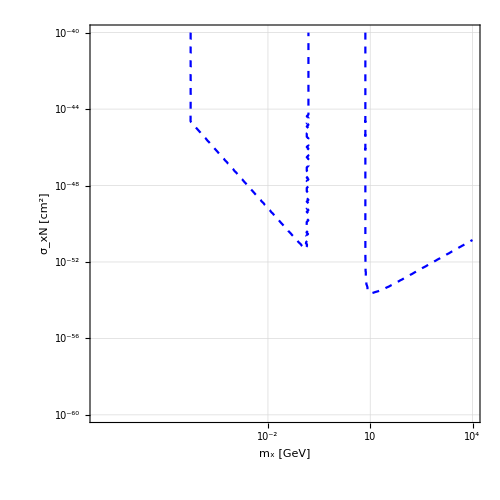

```mathematica
ContourPlot[{totcapuni[10^x,10^y]==NchBoson[10^x]+NxBEC[10^x,10^5]},{x,-7,4},{y,-44,-64},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,GridLines->Automatic,FrameTicks->myticks]
```

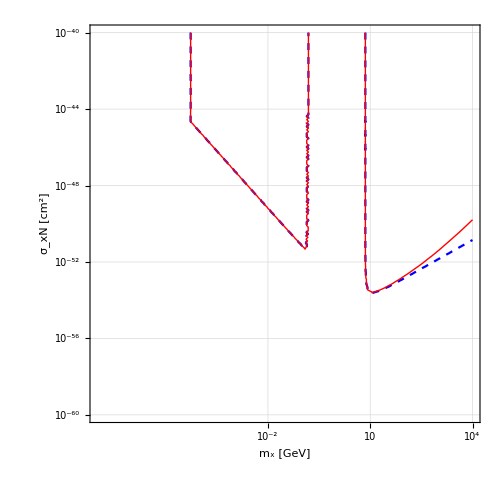

```mathematica
ContourPlot[{totcapuni[10^x,10^y]==NchBoson[10^x]+NxBEC[10^x,10^5],totcapgen[10^x,10^y,10^-2]==NchBoson[10^x]+NxBEC[10^x,10^5]},{x,-7,4},{y,-44,-64},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,GridLines->Automatic,FrameTicks->myticks]
```

```mathematica
(*DARK HEATING*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*10^3(*in GeV/m^3*)(*Due to Overdensity*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
(*asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;*)
```

```mathematica
(*a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));*)
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
ttherm[mx_?NumericQ,sigma_?NumericQ,T_]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*sigma*kb*T);
```

```mathematica
auni[10,sigmasat]
```

7.18429×10^27

```mathematica
agen[100,sigmasat,1]
```

7.18387×10^26

```mathematica
tage=10^10*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
(*lum[mx_?NumericQ,sigma_?NumericQ]:=  a[mx,sigma]*mx;*)
```

```mathematica
lumuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*mx;
lumgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*mx;
```

```mathematica
lumobs[T_?NumericQ]:=4*π*R^2*T^4*5.67*10^-8*6.242*10^9;(*in GeV*)
```

```mathematica
lumobs[10^4]
```

4.99722×10^27

```mathematica
lumuni[100,sigmasat]
```

7.18413×10^28

```mathematica
lumgen[100,sigmasat,0.1]
```

7.15855×10^28

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data1=Import["xenon.dat","Table"];
(*data2=Import["neutrino_floor.dat","Table"];
data3=Import["darkside50.dat","Table"];
data4=Import["lux.dat","Table"];
*)
(*data6=Import["xenon_v2.dat","Table"];
data7=Import["xenon_v3.dat","Table"];*)
```

```mathematica
data10=Import["contact.dat","Table"];
```

```mathematica
data11=Import["10 MeV.dat","Table"];
```

```mathematica
data12=Import["1 MeV.dat","Table"];
```

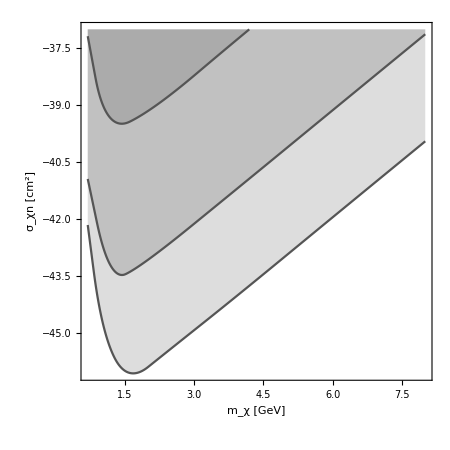

```mathematica
ListPlot[{Table[{Log10[data10[[i,1]]],Log10[data10[[i,2]]]},{i,Length[data10]}],Table[{Log10[data11[[i,1]]],Log10[data11[[i,2]]]},{i,Length[data11]}],Table[{Log10[data12[[i,1]]],Log10[data12[[i,2]]]},{i,Length[data12]}]},PlotRange->{{0,6},{-37,-47}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,InterpolationOrder->2]
```

```mathematica
(*data10//Grid*)
```

```mathematica
(*data11//Grid*)
```

```mathematica
(*data12//Grid*)
```

```mathematica
myticks2={{{{10^26,"10^26",{0.020,0}},{9*10^25,"",{0.010,0}},{8*10^25,"",{0.010,0}},{7*10^25,"",{0.010,0}},{6*10^25,"",{0.010,0}},{5*10^25,"",{0.010,0}},{4*10^25,"",{0.010,0}},{3*10^25,"",{0.010,0}},{2*10^25,"",{0.010,0}},{10^25,"10^25",{0.020,0}},{9*10^24,"",{0.010,0}},{8*10^24,"",{0.010,0}},{7*10^24,"",{0.010,0}},{6*10^24,"",{0.010,0}},{5*10^24,"",{0.010,0}},{4*10^24,"",{0.010,0}},{3*10^24,"",{0.010,0}},{2*10^24,"",{0.010,0}},{10^24,"10^24",{0.020,0}},{9*10^23,"",{0.010,0}},{8*10^23,"",{0.010,0}},{7*10^23,"",{0.010,0}},{6*10^23,"",{0.010,0}},{5*10^23,"",{0.010,0}},{4*10^23,"",{0.010,0}},{3*10^23,"",{0.010,0}},{2*10^23,"",{0.010,0}},{10^23,"10^23",{0.020,0}}},None},{{{0,"1",{0.020,0}},{Log10[2],"",{0.010,0}},{Log10[3],"",{0.010,0}},{Log10[4],"",{0.010,0}},{Log10[5],"",{0.010,0}},{Log10[6],"",{0.010,0}},{Log10[7],"",{0.010,0}},{Log10[8],"",{0.010,0}},{Log10[9],"",{0.010,0}},{1,"10",{0.020,0}},{Log10[20],"",{0.010,0}},{Log10[30],"",{0.010,0}},{Log10[40],"",{0.010,0}},{Log10[50],"",{0.010,0}},{Log10[60],"",{0.010,0}},{Log10[70],"",{0.010,0}},{Log10[80],"",{0.010,0}},{Log10[90],"",{0.010,0}},{2,"10^2",{0.020,0}},{Log10[200],"",{0.010,0}},{Log10[300],"",{0.010,0}},{Log10[400],"",{0.010,0}},{Log10[500],"",{0.010,0}},{Log10[600],"",{0.010,0}},{Log10[700],"",{0.010,0}},{Log10[800],"",{0.010,0}},{Log10[900],"",{0.010,0}},{3,"10^3",{0.020,0}},{Log10[2000],"",{0.010,0}},{Log10[3000],"",{0.010,0}},{Log10[4000],"",{0.010,0}},{Log10[5000],"",{0.010,0}},{Log10[6000],"",{0.010,0}},{Log10[7000],"",{0.010,0}},{Log10[8000],"",{0.010,0}},{Log10[9000],"",{0.010,0}},{4,"10^4",{0.020,0}},{Log10[2*10^4],"",{0.010,0}},{Log10[3*10^4],"",{0.010,0}},{Log10[4*10^4],"",{0.010,0}},{Log10[5*10^4],"",{0.010,0}},{Log10[6*10^4],"",{0.010,0}},{Log10[7*10^4],"",{0.010,0}},{Log10[8*10^4],"",{0.010,0}},{Log10[9*10^4],"",{0.010,0}},{5,"10^5",{0.020,0}},{Log10[2*10^5],"",{0.010,0}},{Log10[3*10^5],"",{0.010,0}},{Log10[4*10^5],"",{0.010,0}},{Log10[5*10^5],"",{0.010,0}},{Log10[6*10^5],"",{0.010,0}},{Log10[7*10^5],"",{0.010,0}},{Log10[8*10^5],"",{0.010,0}},{Log10[9*10^5],"",{0.010,0}},{6,"10^6",{0.020,0}},{7,"10^7",{0.020,0}},{8,"10^8",{0.020,0}}},None}};
```

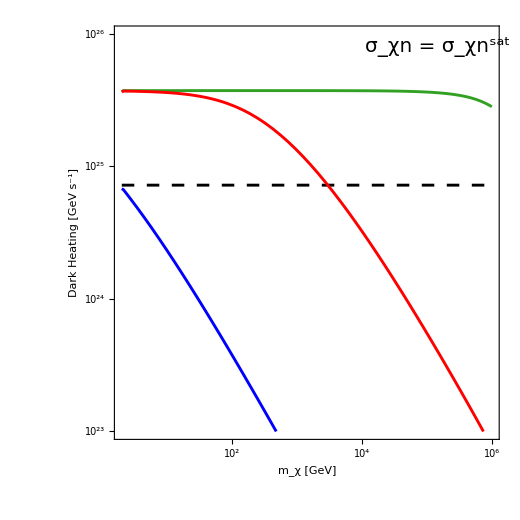

```mathematica
wo1=Show[LogPlot[{lumobs[1950]},{x,Log10[2],6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotRange->{{Log10[2],6},{10^23,10^26}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Row[{Style["Dark Heating [GeV ",FontSize->20,Bold],Style[Superscript["s","-1"],FontSize->20,Bold],Style["]",FontSize->20,Bold]}]},ImageSize->520,AspectRatio->1,FrameTicks->myticks2,Epilog->Text[Style["σ_χn = σ_χn^sat",Black,20],Scaled[{.84,.95}]]],LogPlot[{0.4/10^3*1.3*lumuni[10^x,sigmasat]},{x,Log10[2],6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotRange->{{Log10[2],6},{10^23,10^26}},PlotStyle->Directive[RGBColor["#32A123"],Thickness[0.004]],FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["Dark Luminosity",FontSize->20,Bold]},ImageSize->520,AspectRatio->1],LogPlot[{0.4/10^3*1.3*lumgen[10^x,sigmasat,0.01]},{x,Log10[2],6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotRange->{{Log10[2],6},{10^23,10^26}},PlotStyle->{Directive[Red,Thickness[0.004]]},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["Dark luminosity",FontSize->20,Bold]},ImageSize->520,AspectRatio->1],LogPlot[{0.4/10^3*1.3*lumgen[10^x,sigmasat,0.00025]},{x,Log10[2],6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotRange->{{Log10[2],6},{10^23,10^26}},PlotStyle->{Directive[Blue,Thickness[0.004]]},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["Dark luminosity",FontSize->20,Bold]},ImageSize->520,AspectRatio->1],Graphics[Rotate[Text[Style["m_ϕ → ∞",Darker[Green],FontSize->16],Scaled[{0.85,0.80}]],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 10 MeV",Red,FontSize->16],Scaled[{0.7,0.20}]],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 0.25 MeV",Blue,FontSize->16],Scaled[{0.2,0.10}]],0 Degree]],Graphics[Rotate[Text[Style["Observed \n Luminosity",Darker[Black],FontSize->16],Scaled[{0.85,0.56}]],0 Degree]]]
```

```mathematica
Export["washout_heating.pdf",wo1];
```

```mathematica
myticks={{{{-44,"10^-40",{0.020,0}},{Log10[9*10^-45],"",{0.010,0}},{Log10[8*10^-45],"",{0.010,0}},{Log10[7*10^-45],"",{0.010,0}},{Log10[6*10^-45],"",{0.010,0}},{Log10[5*10^-45],"",{0.010,0}},{Log10[4*10^-45],"",{0.010,0}},{Log10[3*10^-45],"",{0.010,0}},{Log10[2*10^-45],"",{0.010,0}},{-45,"10^-41",{0.020,0}},{Log10[9*10^-46],"",{0.010,0}},{Log10[8*10^-46],"",{0.010,0}},{Log10[7*10^-46],"",{0.010,0}},{Log10[6*10^-46],"",{0.010,0}},{Log10[5*10^-46],"",{0.010,0}},{Log10[4*10^-46],"",{0.010,0}},{Log10[3*10^-46],"",{0.010,0}},{Log10[2*10^-46],"",{0.010,0}},{-46,"10^-42",{0.020,0}},{Log10[9*10^-47],"",{0.010,0}},{Log10[8*10^-47],"",{0.010,0}},{Log10[7*10^-47],"",{0.010,0}},{Log10[6*10^-47],"",{0.010,0}},{Log10[5*10^-47],"",{0.010,0}},{Log10[4*10^-47],"",{0.010,0}},{Log10[3*10^-47],"",{0.010,0}},{Log10[2*10^-47],"",{0.010,0}},{-47,"10^-43",{0.020,0}},{Log10[9*10^-48],"",{0.010,0}},{Log10[8*10^-48],"",{0.010,0}},{Log10[7*10^-48],"",{0.010,0}},{Log10[6*10^-48],"",{0.010,0}},{Log10[5*10^-48],"",{0.010,0}},{Log10[4*10^-48],"",{0.010,0}},{Log10[3*10^-48],"",{0.010,0}},{Log10[2*10^-48],"",{0.010,0}},{-48,"10^-44",{0.020,0}},{Log10[9*10^-49],"",{0.010,0}},{Log10[8*10^-49],"",{0.010,0}},{Log10[7*10^-49],"",{0.010,0}},{Log10[6*10^-49],"",{0.010,0}},{Log10[5*10^-49],"",{0.010,0}},{Log10[4*10^-49],"",{0.010,0}},{Log10[3*10^-49],"",{0.010,0}},{Log10[2*10^-49],"",{0.010,0}},{-49,"10^-45",{0.020,0}},{Log10[9*10^-50],"",{0.010,0}},{Log10[8*10^-50],"",{0.010,0}},{Log10[7*10^-50],"",{0.010,0}},{Log10[6*10^-50],"",{0.010,0}},{Log10[5*10^-50],"",{0.010,0}},{Log10[4*10^-50],"",{0.010,0}},{Log10[3*10^-50],"",{0.010,0}},{Log10[2*10^-50],"",{0.010,0}},{-50,"10^-46",{0.020,0}},{Log10[9*10^-51],"",{0.010,0}},{Log10[8*10^-51],"",{0.010,0}},{Log10[7*10^-51],"",{0.010,0}},{Log10[6*10^-51],"",{0.010,0}},{Log10[5*10^-51],"",{0.010,0}},{Log10[4*10^-51],"",{0.010,0}},{Log10[3*10^-51],"",{0.010,0}},{Log10[2*10^-51],"",{0.010,0}},{-51,"10^-47",{0.020,0}},{Log10[9*10^-52],"",{0.010,0}},{Log10[8*10^-52],"",{0.010,0}},{Log10[7*10^-52],"",{0.010,0}},{Log10[6*10^-52],"",{0.010,0}},{Log10[5*10^-52],"",{0.010,0}},{Log10[4*10^-52],"",{0.010,0}},{Log10[3*10^-52],"",{0.010,0}},{Log10[2*10^-52],"",{0.010,0}},{-52,"10^-48",{0.020,0}}},None},{{{0,"1",{0.020,0}},{Log10[2],"",{0.010,0}},{Log10[3],"",{0.010,0}},{Log10[4],"",{0.010,0}},{Log10[5],"",{0.010,0}},{Log10[6],"",{0.010,0}},{Log10[7],"",{0.010,0}},{Log10[8],"",{0.010,0}},{Log10[9],"",{0.010,0}},{1,"10",{0.020,0}},{Log10[20],"",{0.010,0}},{Log10[30],"",{0.010,0}},{Log10[40],"",{0.010,0}},{Log10[50],"",{0.010,0}},{Log10[60],"",{0.010,0}},{Log10[70],"",{0.010,0}},{Log10[80],"",{0.010,0}},{Log10[90],"",{0.010,0}},{2,"10^2",{0.020,0}},{Log10[200],"",{0.010,0}},{Log10[300],"",{0.010,0}},{Log10[400],"",{0.010,0}},{Log10[500],"",{0.010,0}},{Log10[600],"",{0.010,0}},{Log10[700],"",{0.010,0}},{Log10[800],"",{0.010,0}},{Log10[900],"",{0.010,0}},{3,"10^3",{0.020,0}},{Log10[2000],"",{0.010,0}},{Log10[3000],"",{0.010,0}},{Log10[4000],"",{0.010,0}},{Log10[5000],"",{0.010,0}},{Log10[6000],"",{0.010,0}},{Log10[7000],"",{0.010,0}},{Log10[8000],"",{0.010,0}},{Log10[9000],"",{0.010,0}},{4,"10^4",{0.020,0}},{Log10[2*10^4],"",{0.010,0}},{Log10[3*10^4],"",{0.010,0}},{Log10[4*10^4],"",{0.010,0}},{Log10[5*10^4],"",{0.010,0}},{Log10[6*10^4],"",{0.010,0}},{Log10[7*10^4],"",{0.010,0}},{Log10[8*10^4],"",{0.010,0}},{Log10[9*10^4],"",{0.010,0}},{5,"10^5",{0.020,0}},{Log10[2*10^5],"",{0.010,0}},{Log10[3*10^5],"",{0.010,0}},{Log10[4*10^5],"",{0.010,0}},{Log10[5*10^5],"",{0.010,0}},{Log10[6*10^5],"",{0.010,0}},{Log10[7*10^5],"",{0.010,0}},{Log10[8*10^5],"",{0.010,0}},{Log10[9*10^5],"",{0.010,0}},{6,"10^6",{0.020,0}},{7,"10^7",{0.020,0}},{8,"10^8",{0.020,0}}},None}};
```

```mathematica
(*Show[RegionPlot[{ttherm[10^x,10^y,10^4]≥  tage},{x,Log10[2],6},{y,-44,-60},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Pink],PlotStyle->Lighter[Pink],Mesh->50,FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],ContourPlot[{lumuni[10^x,10^y]==lumobs[10^4],lumgen[10^x,10^y,1]==lumobs[10^4],lumgen[10^x,10^y,0.1]==lumobs[10^4],lumgen[10^x,10^y,10^-2]==lumobs[10^4]},{x,0,6},{y,-44,-60},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green},{Thick,Purple}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks,PlotLegends->Placed[LineLegend[{"Uniform","m_ϕ = 1 GeV","m_ϕ = 0.1 GeV","m_ϕ = 0.01 GeV"},LabelStyle->{FontSize->16}],{0.25,0.30}]],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}],Table[{Log10[data4[[i,1]]],-data4[[i,2]]-4},{i,Length[data4]}]},PlotRange->{{0,3},{-44,-64}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{4.2,-57.83}],0 Degree]]]//Quiet*)
```

```mathematica
(*Show[RegionPlot[{ttherm[10^x,10^y,1750]≥  tage},{x,Log10[2],6},{y,-44,-60},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Pink],PlotStyle->Lighter[Pink],Mesh->50,FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],ContourPlot[{0.4/10^3*lumuni[10^x,10^y]==lumobs[1750],0.4/10^3*lumgen[10^x,10^y,1]==lumobs[1750],0.4/10^3*lumgen[10^x,10^y,0.1]==lumobs[1750],0.4/10^3*lumgen[10^x,10^y,10^-2]==lumobs[1750]},{x,0,6},{y,-44,-60},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green},{Thick,Purple}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks,PlotLegends->Placed[LineLegend[{"Uniform","m_ϕ = 1 GeV","m_ϕ = 0.1 GeV","m_ϕ = 0.01 GeV"},LabelStyle->{FontSize->16}],{0.25,0.35}]],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}],Table[{Log10[data4[[i,1]]],-data4[[i,2]]-4},{i,Length[data4]}]},PlotRange->{{0,3},{-44,-64}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{4.2,-57.83}],0 Degree]]]//Quiet*)
```

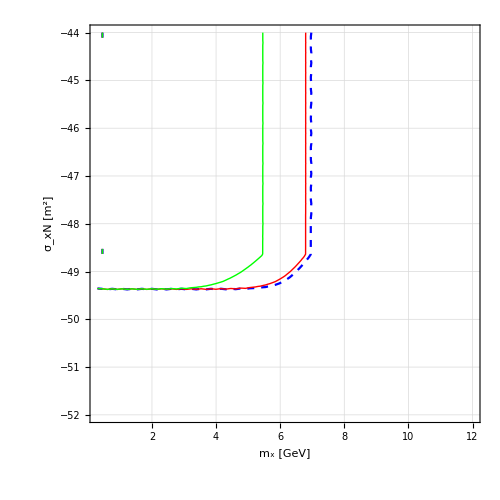

```mathematica
ContourPlot[{0.4/10^3*1.3*lumuni[10^x,10^y]==lumobs[1950],0.4/10^3*1.3*lumgen[10^x,10^y,1]==lumobs[1950],0.4/10^3*1.3*lumgen[10^x,10^y,0.1]==lumobs[1950],0.4/10^3*1.3*lumgen[10^x,10^y,2.5*10^-4]==lumobs[1950]},{x,Log10[2],12},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green},{Thick,Purple}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,GridLines->Automatic]//Quiet
```

```mathematica
(*p=Show[RegionPlot[{0.4/10^3*lumuni[10^x,10^y]≥  lumobs[1750]},{x,Log10[2],6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,FrameTicks->myticks,ImageSize->500],RegionPlot[{0.4/10^3*lumgen[10^x,10^y,1]≥ lumobs[1750]},{x,0,6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#C4F1BE"],BoundaryStyle->RGBColor["#21295C"],PlotRangePadding->None,ImageSize->500],RegionPlot[{0.4/10^3*lumgen[10^x,10^y,0.1]≥ lumobs[1750]},{x,0,6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#FBF9C5"],BoundaryStyle->RGBColor["#21295C"],PlotRangePadding->None,ImageSize->500],RegionPlot[{0.4/10^3*lumgen[10^x,10^y,0.01]≥ lumobs[1750]},{x,0,6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#F6A18E"],BoundaryStyle->RGBColor["#21295C"],PlotRangePadding->None,ImageSize->500],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}]},PlotRange->{{0,3},{-44,-52}},PlotStyle->Directive[Darker[Gray],Thickness[0.006]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Plot[Log10[sigmasat],{x,Log10[2],6},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]],Graphics[Rotate[Text[Style["XENON-1T",Darker[Black],FontSize->16],{2.9,-50.23}],0 Degree]],Graphics[Rotate[Text[Style["Saturation limit",Darker[Black],FontSize->16],{2.2,-48.33}],0 Degree]],Graphics[Rotate[Text[Style["Uniform",Darker[Blue],FontSize->16],{5.4,-49.63}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 10 MeV",RGBColor["#E83A12"],FontSize->16],{2.4,-45.63}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 100 MeV",RGBColor["#B5AE0C"],FontSize->16],{4.5,-45.63}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 1 GeV",RGBColor["#32A123"],FontSize->16],{5.8,-45.33}],90 Degree]]]//Quiet*)
```

```mathematica
(*pv2=Show[Plot[-42,{x,0,6},PlotRange->{{Log10[2],6},{-44,-52}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},ImageSize->520,FrameTicks->myticks,AspectRatio->1],RegionPlot[{0.4/10^3*1.3*lumuni[10^x,10^y]≥  lumobs[1950]},{x,Log10[2],6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,FrameTicks->myticks,ImageSize->500],RegionPlot[{0.4/10^3*1.3*lumgen[10^x,10^y,1]≥ lumobs[1950]},{x,0,6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#C4F1BE"],BoundaryStyle->RGBColor["#32A123"],PlotRangePadding->None,ImageSize->500],RegionPlot[{0.4/10^3*1.3*lumgen[10^x,10^y,0.1]≥ lumobs[1950]},{x,0,6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#FBF9C5"],BoundaryStyle->RGBColor["#C7C00E"],PlotRangePadding->None,ImageSize->500],RegionPlot[{0.4/10^3*1.3*lumgen[10^x,10^y,0.01]≥ lumobs[1950]},{x,0,6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#F6A18E"],BoundaryStyle->RGBColor["#D63511"],PlotRangePadding->None,ImageSize->500],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}]},PlotRange->{{0,3},{-44,-52}},PlotStyle->Directive[Darker[Gray],Thickness[0.006]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Plot[Log10[sigmasat],{x,Log10[2],6},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]],Graphics[Rotate[Text[Style["XENON-1T",Darker[Black],FontSize->16],{2.9,-50.23}],0 Degree]],Graphics[Rotate[Text[Style["Saturation limit",Darker[Black],FontSize->16],{2.2,-48.33}],0 Degree]],Graphics[Rotate[Text[Style["Uniform",Darker[Blue],FontSize->16],{5.4,-49.63}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 10 MeV",RGBColor["#C43110"],FontSize->16],{2.4,-45.63}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 100 MeV",RGBColor["#B5AE0C"],FontSize->16],{4.5,-45.63}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 1 GeV",RGBColor["#32A123"],FontSize->16],{5.75,-45.33}],90 Degree]]]//Quiet*)
```

```mathematica
(*Plot[-42,{x,0,6},PlotRange->{{Log10[2],6},{-44,-52}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},ImageSize->520,FrameTicks->myticks,AspectRatio->1]*)
```

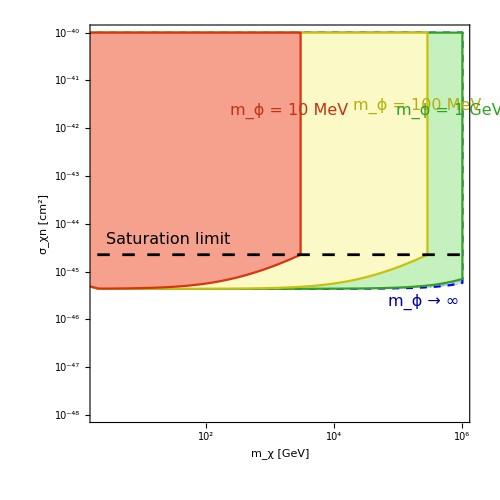

```mathematica
pv3=Show[RegionPlot[{0.4/10^3*1.3*lumuni[10^x,10^y]≥  lumobs[1950]},{x,Log10[2],6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["σ_χn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,FrameTicks->myticks,ImageSize->500],RegionPlot[{0.4/10^3*1.3*lumgen[10^x,10^y,1]≥ lumobs[1950]},{x,0,6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->Directive[RGBColor["#C4F1BE"]],BoundaryStyle->RGBColor["#32A123"],PlotRangePadding->None,ImageSize->500],RegionPlot[{0.4/10^3*1.3*lumgen[10^x,10^y,0.1]≥ lumobs[1950]},{x,0,6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->Directive[RGBColor["#FBF9C5"]],BoundaryStyle->RGBColor["#C7C00E"],PlotRangePadding->None,ImageSize->500],RegionPlot[{0.4/10^3*1.3*lumgen[10^x,10^y,0.01]≥ lumobs[1950]},{x,0,6},{y,-44,-52},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->Directive[RGBColor["#F6A18E"]],BoundaryStyle->RGBColor["#D63511"],PlotRangePadding->None,ImageSize->500],Plot[Log10[sigmasat],{x,Log10[2],6},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]],Graphics[Rotate[Text[Style["Saturation limit",Darker[Black],FontSize->16],{1.4,-48.33}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ → ∞",Darker[Blue],FontSize->16],{5.4,-49.63}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 10 MeV",RGBColor["#C43110"],FontSize->16],{3.3,-45.63}],90 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 100 MeV",RGBColor["#B5AE0C"],FontSize->16],{5.3,-45.53}],90 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 1 GeV",RGBColor["#32A123"],FontSize->16],{5.8,-45.63}],90 Degree]]]//Quiet
```

```mathematica
(*pv4=Show[RegionPlot[{0.4/10^3*1.3*lumuni[10^x,10^(y-4)]≥  lumobs[1950]},{x,Log10[2],6},{y,-35,-47},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["σ_χn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,ImageSize->600],RegionPlot[{0.4/10^3*1.3*lumgen[10^x,10^(y-4),1]≥ lumobs[1950]},{x,0,6},{y,-35,-46},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->Directive[RGBColor["#C4F1BE"]],BoundaryStyle->RGBColor["#32A123"],PlotRangePadding->None,ImageSize->500],RegionPlot[{0.4/10^3*1.3*lumgen[10^x,10^(y-4),0.1]≥ lumobs[1950]},{x,0,6},{y,-35,-46},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->Directive[RGBColor["#FBF9C5"]],BoundaryStyle->RGBColor["#C7C00E"],PlotRangePadding->None,ImageSize->500],RegionPlot[{0.4/10^3*1.3*lumgen[10^x,10^(y-4),0.001]≥ lumobs[1950]},{x,0,6},{y,-35,-46},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->Directive[RGBColor["#F6A18E"]],BoundaryStyle->RGBColor["#D63511"],PlotRangePadding->None,ImageSize->500],Plot[Log10[10^4*sigmasat],{x,Log10[2],6},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]]]//Quiet*)
```

```mathematica
(*Export["region.pdf",Show[pv3,Prolog->{Opacity[1],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]];*)
```

```mathematica
Export["heating.pdf",pv3];
```

```mathematica
Export["heating.pdf",pv2];
```

```mathematica
Export["heating.pdf",p];
```

```mathematica
(*//////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////*)
```

```mathematica
(*CHECKS*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
c=3*10^8;
```

```mathematica
(*vesc=(1.8*10^8)/((1+0.75*((1.8*10^8)^2)/c^2)^0.5)(*in m/sec*);*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
vesc=1.8*10^8;
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];(*gravitational blueshift is included*)
```

```mathematica
auni[10,sigmasat]
```

2.87372×10^24

```mathematica
((2.873715278378839*^24)/(2.262766703652506*^24))^-1
```

0.787401

```mathematica
0.61/2.87
```

0.212544

```mathematica
1/(1-(vesc/(3*10^8))^2)
```

1.49315

```mathematica
(*//////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////*)
```

```mathematica
(*PSR J0437-4715*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
(*ttherm[mx_?NumericQ,sigma_?NumericQ,T_]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*sigma*kb*T);*)
```

```mathematica
auni[100,sigmasat]
```

2.87365×10^23

```mathematica
agen[100,sigmasat,0.1]
```

2.86342×10^23

```mathematica
tage=6.69*10^9*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
sigmatherm[mx_?NumericQ,T_?NumericQ]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*tage*kb*T);
```

```mathematica
totcapuni[10^5,sigmatherm[10^5,2.1*10^6]]
```

1.86268×10^31

```mathematica
totcapgen[100,sigmasat,0.01]
```

4.69646×10^40

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27);
(*NxBEC[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*2.612*((mx*T*8.62*10^-14)/(2*π))^1.5*(5.62*10^15)^3;*)
Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
NchFermion[mx_?NumericQ]:=Mpl^3/mx^3;
```

```mathematica
GN=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
cns=0.17;
λ=0.25;
```

```mathematica
mcrit=1/GN*(cns^3/(74*π*4*π*λ*ρ*5.62*10^26*(1.98*10^-16)^3))^0.25;(*critical mass for BH evaporation in GeV*)
```

```mathematica
mcrit
```

2.71619×10^37

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data1=Import["xenon.dat","Table"];


FindRoot[10^x*Max[Nself[10^x,2.1*10^6],NchBoson[10^x]]==mcrit,{x,0}]//Quiet(*Without BEC*)
```

{x→7.48568}

```mathematica
FindRoot[10^x*Max[Nself[10^x,2.1*10^6],NchFermion[10^x]]==mcrit,{x,0}]//Quiet(*Without BEC*)
```

{x→9.91315}

```mathematica
10^7.48568
```

3.05971×10^7

```mathematica
10^9.91315
```

8.18748×10^9

```mathematica
NchBosonself[mx_?NumericQ,λ_?NumericQ]:=2/π*Mpl^2/mx^2*(1+λ/(32*π)*Mpl^2/mx^2)^0.5;
```

```mathematica
NchBosonself2[mx_?NumericQ,sigmadmdm_]:=2/π*Mpl^2/mx^2*(1+((64*π*sigmadmdm)^0.5*mx*5.06*10^15)/(32*π)*Mpl^2/mx^2)^0.5;
```

```mathematica
myticks={{{{-44,"10^-40",{0.020,0}},{Log10[9*10^-45],"",{0.010,0}},{Log10[8*10^-45],"",{0.010,0}},{Log10[7*10^-45],"",{0.010,0}},{Log10[6*10^-45],"",{0.010,0}},{Log10[5*10^-45],"",{0.010,0}},{Log10[4*10^-45],"",{0.010,0}},{Log10[3*10^-45],"",{0.010,0}},{Log10[2*10^-45],"",{0.010,0}},{-45,"10^-41",{0.020,0}},{Log10[9*10^-46],"",{0.010,0}},{Log10[8*10^-46],"",{0.010,0}},{Log10[7*10^-46],"",{0.010,0}},{Log10[6*10^-46],"",{0.010,0}},{Log10[5*10^-46],"",{0.010,0}},{Log10[4*10^-46],"",{0.010,0}},{Log10[3*10^-46],"",{0.010,0}},{Log10[2*10^-46],"",{0.010,0}},{-46,"10^-42",{0.020,0}},{Log10[9*10^-47],"",{0.010,0}},{Log10[8*10^-47],"",{0.010,0}},{Log10[7*10^-47],"",{0.010,0}},{Log10[6*10^-47],"",{0.010,0}},{Log10[5*10^-47],"",{0.010,0}},{Log10[4*10^-47],"",{0.010,0}},{Log10[3*10^-47],"",{0.010,0}},{Log10[2*10^-47],"",{0.010,0}},{-47,"10^-43",{0.020,0}},{Log10[9*10^-48],"",{0.010,0}},{Log10[8*10^-48],"",{0.010,0}},{Log10[7*10^-48],"",{0.010,0}},{Log10[6*10^-48],"",{0.010,0}},{Log10[5*10^-48],"",{0.010,0}},{Log10[4*10^-48],"",{0.010,0}},{Log10[3*10^-48],"",{0.010,0}},{Log10[2*10^-48],"",{0.010,0}},{-48,"10^-44",{0.020,0}},{Log10[9*10^-49],"",{0.010,0}},{Log10[8*10^-49],"",{0.010,0}},{Log10[7*10^-49],"",{0.010,0}},{Log10[6*10^-49],"",{0.010,0}},{Log10[5*10^-49],"",{0.010,0}},{Log10[4*10^-49],"",{0.010,0}},{Log10[3*10^-49],"",{0.010,0}},{Log10[2*10^-49],"",{0.010,0}},{-49,"10^-45",{0.020,0}},{Log10[9*10^-50],"",{0.010,0}},{Log10[8*10^-50],"",{0.010,0}},{Log10[7*10^-50],"",{0.010,0}},{Log10[6*10^-50],"",{0.010,0}},{Log10[5*10^-50],"",{0.010,0}},{Log10[4*10^-50],"",{0.010,0}},{Log10[3*10^-50],"",{0.010,0}},{Log10[2*10^-50],"",{0.010,0}},{-50,"10^-46",{0.020,0}},{Log10[9*10^-51],"",{0.010,0}},{Log10[8*10^-51],"",{0.010,0}},{Log10[7*10^-51],"",{0.010,0}},{Log10[6*10^-51],"",{0.010,0}},{Log10[5*10^-51],"",{0.010,0}},{Log10[4*10^-51],"",{0.010,0}},{Log10[3*10^-51],"",{0.010,0}},{Log10[2*10^-51],"",{0.010,0}},{-51,"10^-47",{0.020,0}},{Log10[9*10^-52],"",{0.010,0}},{Log10[8*10^-52],"",{0.010,0}},{Log10[7*10^-52],"",{0.010,0}},{Log10[6*10^-52],"",{0.010,0}},{Log10[5*10^-52],"",{0.010,0}},{Log10[4*10^-52],"",{0.010,0}},{Log10[3*10^-52],"",{0.010,0}},{Log10[2*10^-52],"",{0.010,0}},{-52,"10^-48",{0.020,0}}},None},{{{0,"1",{0.020,0}},{Log10[2],"",{0.010,0}},{Log10[3],"",{0.010,0}},{Log10[4],"",{0.010,0}},{Log10[5],"",{0.010,0}},{Log10[6],"",{0.010,0}},{Log10[7],"",{0.010,0}},{Log10[8],"",{0.010,0}},{Log10[9],"",{0.010,0}},{1,"10",{0.020,0}},{Log10[20],"",{0.010,0}},{Log10[30],"",{0.010,0}},{Log10[40],"",{0.010,0}},{Log10[50],"",{0.010,0}},{Log10[60],"",{0.010,0}},{Log10[70],"",{0.010,0}},{Log10[80],"",{0.010,0}},{Log10[90],"",{0.010,0}},{2,"10^2",{0.020,0}},{Log10[200],"",{0.010,0}},{Log10[300],"",{0.010,0}},{Log10[400],"",{0.010,0}},{Log10[500],"",{0.010,0}},{Log10[600],"",{0.010,0}},{Log10[700],"",{0.010,0}},{Log10[800],"",{0.010,0}},{Log10[900],"",{0.010,0}},{3,"10^3",{0.020,0}},{Log10[2000],"",{0.010,0}},{Log10[3000],"",{0.010,0}},{Log10[4000],"",{0.010,0}},{Log10[5000],"",{0.010,0}},{Log10[6000],"",{0.010,0}},{Log10[7000],"",{0.010,0}},{Log10[8000],"",{0.010,0}},{Log10[9000],"",{0.010,0}},{4,"10^4",{0.020,0}},{Log10[2*10^4],"",{0.010,0}},{Log10[3*10^4],"",{0.010,0}},{Log10[4*10^4],"",{0.010,0}},{Log10[5*10^4],"",{0.010,0}},{Log10[6*10^4],"",{0.010,0}},{Log10[7*10^4],"",{0.010,0}},{Log10[8*10^4],"",{0.010,0}},{Log10[9*10^4],"",{0.010,0}},{5,"10^5",{0.020,0}},{Log10[2*10^5],"",{0.010,0}},{Log10[3*10^5],"",{0.010,0}},{Log10[4*10^5],"",{0.010,0}},{Log10[5*10^5],"",{0.010,0}},{Log10[6*10^5],"",{0.010,0}},{Log10[7*10^5],"",{0.010,0}},{Log10[8*10^5],"",{0.010,0}},{Log10[9*10^5],"",{0.010,0}},{6,"10^6",{0.020,0}},{7,"10^7",{0.020,0}},{8,"10^8",{0.020,0}}},None}};
```

```mathematica
myticks2={{{{10^43,"10^43",{0.020,0}},{10^42,"",{0.010,0}},{10^41,"",{0.010,0}},{10^40,"",{0.010,0}},{10^39,"",{0.010,0}},{10^38,"10^38",{0.020,0}},{10^37,"",{0.010,0}},{10^36,"",{0.010,0}},{10^35,"",{0.010,0}},{10^34,"",{0.010,0}},{10^33,"10^33",{0.020,0}},{10^32,"",{0.010,0}},{10^31,"",{0.010,0}},{10^30,"",{0.010,0}},{10^29,"",{0.010,0}},{10^28,"10^28",{0.020,0}},{10^27,"",{0.010,0}},{10^26,"",{0.010,0}},{10^25,"",{0.010,0}},{10^24,"",{0.010,0}},{10^23,"10^23",{0.010,0}}},None},{{{0,"1",{0.020,0}},{Log10[2],"",{0.010,0}},{Log10[3],"",{0.010,0}},{Log10[4],"",{0.010,0}},{Log10[5],"",{0.010,0}},{Log10[6],"",{0.010,0}},{Log10[7],"",{0.010,0}},{Log10[8],"",{0.010,0}},{Log10[9],"",{0.010,0}},{1,"10",{0.020,0}},{Log10[20],"",{0.010,0}},{Log10[30],"",{0.010,0}},{Log10[40],"",{0.010,0}},{Log10[50],"",{0.010,0}},{Log10[60],"",{0.010,0}},{Log10[70],"",{0.010,0}},{Log10[80],"",{0.010,0}},{Log10[90],"",{0.010,0}},{2,"10^2",{0.020,0}},{Log10[200],"",{0.010,0}},{Log10[300],"",{0.010,0}},{Log10[400],"",{0.010,0}},{Log10[500],"",{0.010,0}},{Log10[600],"",{0.010,0}},{Log10[700],"",{0.010,0}},{Log10[800],"",{0.010,0}},{Log10[900],"",{0.010,0}},{3,"10^3",{0.020,0}},{Log10[2000],"",{0.010,0}},{Log10[3000],"",{0.010,0}},{Log10[4000],"",{0.010,0}},{Log10[5000],"",{0.010,0}},{Log10[6000],"",{0.010,0}},{Log10[7000],"",{0.010,0}},{Log10[8000],"",{0.010,0}},{Log10[9000],"",{0.010,0}},{4,"10^4",{0.020,0}},{Log10[2*10^4],"",{0.010,0}},{Log10[3*10^4],"",{0.010,0}},{Log10[4*10^4],"",{0.010,0}},{Log10[5*10^4],"",{0.010,0}},{Log10[6*10^4],"",{0.010,0}},{Log10[7*10^4],"",{0.010,0}},{Log10[8*10^4],"",{0.010,0}},{Log10[9*10^4],"",{0.010,0}},{5,"10^5",{0.020,0}},{Log10[2*10^5],"",{0.010,0}},{Log10[3*10^5],"",{0.010,0}},{Log10[4*10^5],"",{0.010,0}},{Log10[5*10^5],"",{0.010,0}},{Log10[6*10^5],"",{0.010,0}},{Log10[7*10^5],"",{0.010,0}},{Log10[8*10^5],"",{0.010,0}},{Log10[9*10^5],"",{0.010,0}},{6,"10^6",{0.020,0}},{7,"10^7",{0.020,0}},{8,"10^8",{0.020,0}}},None}};
```

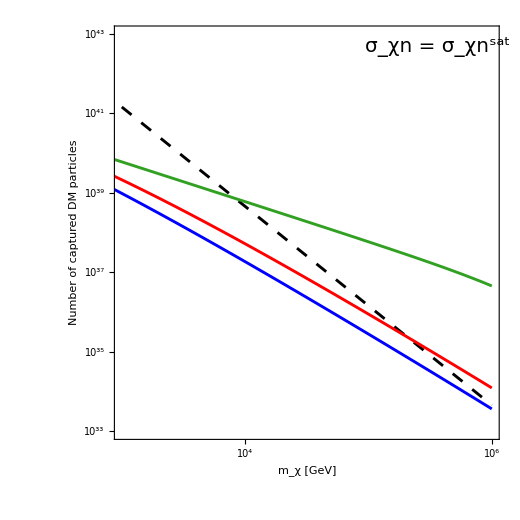

```mathematica
wo2=Show[LogPlot[{Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,3,6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],PlotRange->{{3,6},{10^33,10^43}},FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["Number of captured DM particles",FontSize->20,Bold]},ImageSize->520,AspectRatio->1,FrameTicks->myticks2,Epilog->Text[Style["σ_χn = σ_χn^sat",Black,20],Scaled[{.84,.95}]]],LogPlot[{totcapuni[10^x,sigmasat]},{x,0,6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotStyle->Directive[RGBColor["#32A123"],Thickness[0.004]],FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["Number of captured DM particles",FontSize->20,Bold]},ImageSize->520,AspectRatio->1,Epilog->Text[Style["σ_χn = σ_χn^sat",Black,20],Scaled[{.84,.95}]]],LogPlot[{totcapgen[10^x,sigmasat,0.01]},{x,0,6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotStyle->{Directive[Red,Thickness[0.004]]},FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["Number of captured DM particles",FontSize->20,Bold]},ImageSize->520,AspectRatio->1,Epilog->Text[Style["σ_χn = σ_χn^sat",Black,20],Scaled[{.84,.95}]]],LogPlot[{totcapgen[10^x,sigmasat,0.005]},{x,0,6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotStyle->{Directive[Blue,Thickness[0.004]]},FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["Number of captured DM particles",FontSize->20,Bold]},ImageSize->520,AspectRatio->1,Epilog->Text[Style["σ_χn = σ_χn^sat",Black,20],Scaled[{.84,.95}]]],Graphics[Rotate[Text[Style["m_ϕ → ∞",Darker[Green],FontSize->16],Scaled[{0.92,0.45}]],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 10 MeV",Red,FontSize->16],Scaled[{0.89,0.25}]],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 5 MeV",Blue,FontSize->16],Scaled[{0.6,0.20}]],0 Degree]],Graphics[Rotate[Text[Style["Number of DM particles for \n black hole formation",Darker[Black],FontSize->16],Scaled[{0.35,0.75}]],0 Degree]]]//Quiet
```

```mathematica
Export["washout_collapse.pdf",wo2];
```

```mathematica
(*p=Show[RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,1]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#C4F1BE"],BoundaryStyle->RGBColor["#21295C"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.1]≥ Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#FBF9C5"],BoundaryStyle->RGBColor["#21295C"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.01]≥ Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotPoints->30,PlotStyle->RGBColor["#F6A18E"],BoundaryStyle->RGBColor["#21295C"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}]},PlotRange->{{0,6},{-44,-52}},PlotStyle->Directive[Darker[Gray],Thickness[0.006]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->500,AspectRatio->1,Joined->True,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Plot[Log10[sigmasat],{x,0,6},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]],Graphics[Rotate[Text[Style["XENON-1T",Darker[Black],FontSize->16],{2.9,-50.23}],0 Degree]],Graphics[Rotate[Text[Style["Saturation limit",Darker[Black],FontSize->16],{2.2,-48.33}],0 Degree]],Graphics[Rotate[Text[Style["Uniform",Darker[Blue],FontSize->16],{5.0,-50.93}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 10 MeV",RGBColor["#C43110"],FontSize->16],{5.65,-45.33}],90 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 100 MeV",RGBColor["#B5AE0C"],FontSize->16],{4.55,-45.33}],90 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 1 GeV",RGBColor["#32A123"],FontSize->16],{3.75,-45.33}],90 Degree]]]//Quiet*)
```

```mathematica
(*pv2=Show[Plot[-42,{x,0,6},PlotRange->{{0,6},{-44,-52}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},ImageSize->520,FrameTicks->myticks,AspectRatio->1],RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,1]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#C4F1BE"],BoundaryStyle->RGBColor["#32A123"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.1]≥ Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#FBF9C5"],BoundaryStyle->RGBColor["#C7C00E"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.01]≥ Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotPoints->30,PlotStyle->RGBColor["#F6A18E"],BoundaryStyle->RGBColor["#D63511"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}]},PlotRange->{{0,6},{-44,-52}},PlotStyle->Directive[Darker[Gray],Thickness[0.006]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->500,AspectRatio->1,Joined->True,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Plot[Log10[sigmasat],{x,0,6},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]],Graphics[Rotate[Text[Style["XENON-1T",Darker[Black],FontSize->16],{2.84,-50.23}],0 Degree]],Graphics[Rotate[Text[Style["Saturation limit",Darker[Black],FontSize->16],{2.2,-48.33}],0 Degree]],Graphics[Rotate[Text[Style["Uniform",Darker[Blue],FontSize->16],{5.3,-51.47}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 10 MeV",RGBColor["#E83A12"],FontSize->16],{5.65,-45.33}],90 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 100 MeV",RGBColor["#B5AE0C"],FontSize->16],{4.55,-45.33}],90 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 1 GeV",RGBColor["#32A123"],FontSize->16],{3.75,-45.33}],90 Degree]],Graphics[Rotate[Text[Style["~ 1/m_x^(3/2)",Darker[Black],FontSize->16],{4.1,-50.13}],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{3.95,-49},{5.07,-50.72}}]}]]//Quiet*)
```

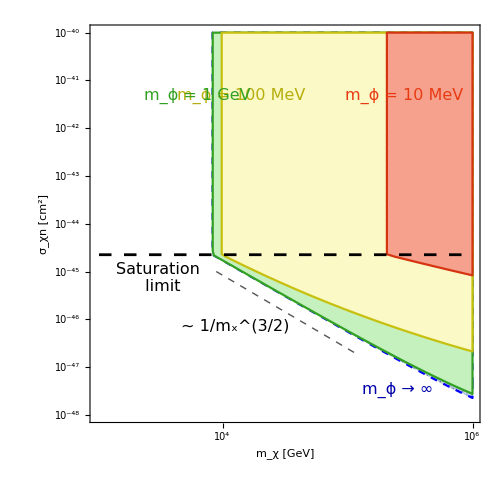

```mathematica
pv3=Show[RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,3,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["σ_χn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,1]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#C4F1BE"],BoundaryStyle->RGBColor["#32A123"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.1]≥ Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#FBF9C5"],BoundaryStyle->RGBColor["#C7C00E"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.01]≥ Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotPoints->30,PlotStyle->RGBColor["#F6A18E"],BoundaryStyle->RGBColor["#D63511"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],Plot[Log10[sigmasat],{x,0,6},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]],Graphics[Rotate[Text[Style["Saturation \n limit",Darker[Black],FontSize->16],{3.5,-49.13}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ → ∞",Darker[Blue],FontSize->16],{5.4,-51.47}],0 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 10 MeV",RGBColor["#E83A12"],FontSize->16],{5.45,-45.33}],90 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 100 MeV",RGBColor["#B5AE0C"],FontSize->16],{4.15,-45.33}],90 Degree]],Graphics[Rotate[Text[Style["m_ϕ = 1 GeV",RGBColor["#32A123"],FontSize->16],{3.8,-45.33}],90 Degree]],Graphics[Rotate[Text[Style["~ 1/m_x^(3/2)",Darker[Black],FontSize->16],{4.1,-50.13}],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{3.95,-49},{5.07,-50.72}}]}]]//Quiet
```

```mathematica
Export["Collapse_boson.pdf",pv3];
```

```mathematica
Export["Collapse_boson.pdf",pv2];
```

```mathematica
Export["Collapse_boson.pdf",p];
```

```mathematica
(*p1=Show[RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,ImageSize->520,FrameTicks->myticks],RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBosonself2[10^x,10^-60]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBosonself2[10^x,10^-56]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}]},PlotRange->{{0,3},{-44,-64}},PlotStyle->Directive[Darker[Gray],Thickness[0.006]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Plot[Log10[sigmasat],{x,0,6},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]],Graphics[Rotate[Text[Style["XENON-1T",Darker[Black],FontSize->16],{2.9,-50.23}],0 Degree]],Graphics[Rotate[Text[Style["Saturation limit",Darker[Black],FontSize->16],{2.2,-48.33}],0 Degree]],Graphics[Rotate[Text[Style["σ_xx = 0",Darker[Black],FontSize->16],{3.7,-45.43}],90 Degree]],Graphics[Rotate[Text[Style["σ_xx = 10^-56 cm^2",Darker[Black],FontSize->16],{4.25,-45.23}],90 Degree]],Graphics[Rotate[Text[Style["σ_xx = 10^-52 cm^2",Darker[Black],FontSize->16],{4.95,-45.23}],90 Degree]]]//Quiet*)
```

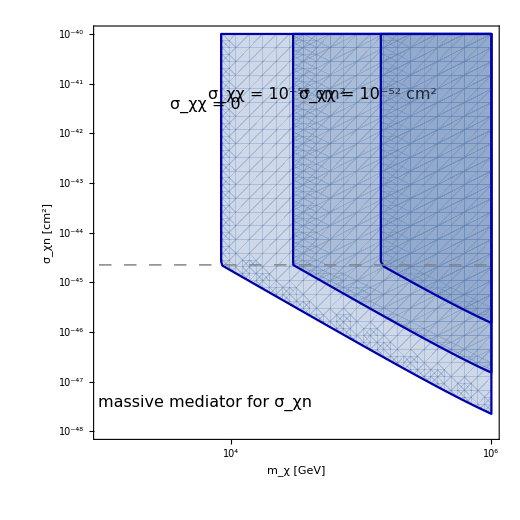

```mathematica
p1=Show[RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,3,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["σ_χn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Darker[Blue]},PlotRangePadding->None,ImageSize->520,FrameTicks->myticks],RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBosonself2[10^x,10^-60]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Darker[Blue]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchBosonself2[10^x,10^-56]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Darker[Blue]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],Plot[Log10[sigmasat],{x,0,6},PlotStyle->Directive[{Dashing[Medium],Gray},Thickness[0.002]]],Graphics[Rotate[Text[Style["σ_χχ = 0",Darker[Black],FontSize->16],{3.8,-45.43}],90 Degree]],Graphics[Rotate[Text[Style["σ_χχ = 10^-56 cm^2",Darker[Black],FontSize->16],{4.35,-45.23}],90 Degree]],Graphics[Rotate[Text[Style["σ_χχ = 10^-52 cm^2",Darker[Black],FontSize->16],{5.05,-45.23}],90 Degree]],Graphics[Rotate[Text[Style[Framed["massive mediator for σ_χn"],Darker[Black],FontSize->16],{3.8,-51.43}],0 Degree]]]//Quiet
```

```mathematica
Export["self_interaction_uniform.pdf",p1];
```

```mathematica
(*p2=Show[RegionPlot[{totcapgen[10^x,10^y,0.1]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->RGBColor["#C7C00E"],PlotStyle->Directive[RGBColor["#FEFD86"],Opacity[0.4]],PlotRangePadding->None,ImageSize->520,FrameTicks->myticks],RegionPlot[{totcapgen[10^x,10^y,0.1]≥Max[ Nself[10^x,2.1*10^6],NchBosonself2[10^x,10^-60]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->RGBColor["#C7C00E"],PlotStyle->Directive[RGBColor["#FEFD86"],Opacity[0.5]],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{totcapgen[10^x,10^y,0.1]≥Max[ Nself[10^x,2.1*10^6],NchBosonself2[10^x,10^-56]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->RGBColor["#C7C00E"],PlotStyle->Directive[RGBColor["#FEFD86"],Opacity[1.0]],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}]},PlotRange->{{0,3},{-44,-64}},PlotStyle->Directive[Darker[Gray],Thickness[0.006]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Plot[Log10[sigmasat],{x,0,6},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]],Graphics[Rotate[Text[Style["XENON-1T",Darker[Black],FontSize->16],{2.9,-50.23}],0 Degree]],Graphics[Rotate[Text[Style["Saturation limit",Darker[Black],FontSize->16],{2.2,-48.33}],0 Degree]],Graphics[Rotate[Text[Style["σ_xx = 0",Darker[Black],FontSize->16],{3.8,-45.23}],90 Degree]],Graphics[Rotate[Text[Style["σ_xx = 10^-56 cm^2",Darker[Black],FontSize->16],{4.5,-45.23}],90 Degree]],Graphics[Rotate[Text[Style["σ_xx = 10^-52 cm^2",Darker[Black],FontSize->16],{5.55,-45.23}],90 Degree]]]//Quiet*)
```

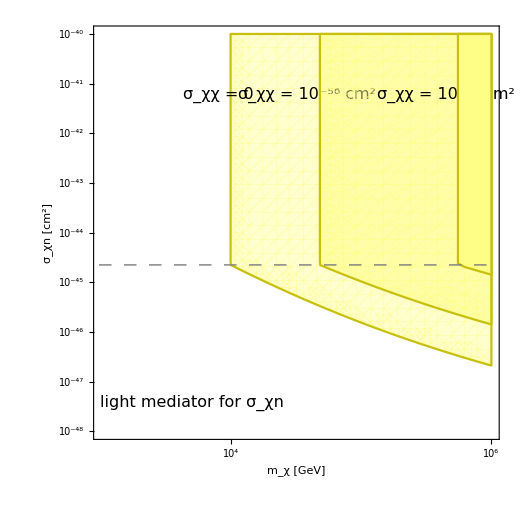

```mathematica
p2=Show[RegionPlot[{totcapgen[10^x,10^y,0.1]≥Max[ Nself[10^x,2.1*10^6],NchBoson[10^x]]},{x,3,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["σ_χn [cm^2]",FontSize->20,Bold]},BoundaryStyle->RGBColor["#C7C00E"],PlotStyle->Directive[RGBColor["#FEFD86"],Opacity[0.4]],PlotRangePadding->None,ImageSize->520,FrameTicks->myticks],RegionPlot[{totcapgen[10^x,10^y,0.1]≥Max[ Nself[10^x,2.1*10^6],NchBosonself2[10^x,10^-60]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->RGBColor["#C7C00E"],PlotStyle->Directive[RGBColor["#FEFD86"],Opacity[0.5]],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{totcapgen[10^x,10^y,0.1]≥Max[ Nself[10^x,2.1*10^6],NchBosonself2[10^x,10^-56]]},{x,0,6},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->RGBColor["#C7C00E"],PlotStyle->Directive[RGBColor["#FEFD86"],Opacity[1.0]],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],Plot[Log10[sigmasat],{x,0,6},PlotStyle->Directive[{Dashing[Medium],Gray},Thickness[0.002]]],Graphics[Rotate[Text[Style["σ_χχ = 0",Darker[Black],FontSize->16],{3.9,-45.23}],90 Degree]],Graphics[Rotate[Text[Style["σ_χχ = 10^-56 cm^2",Darker[Black],FontSize->16],{4.58,-45.23}],90 Degree]],Graphics[Rotate[Text[Style["σ_χχ = 10^-52 cm^2",Darker[Black],FontSize->16],{5.65,-45.23}],90 Degree]],Graphics[Rotate[Text[Style[Framed["light mediator for σ_χn"],Darker[Black],FontSize->16],{3.7,-51.43}],0 Degree]]]//Quiet
```

```mathematica
Export["self_interaction_general.pdf",p2];
```

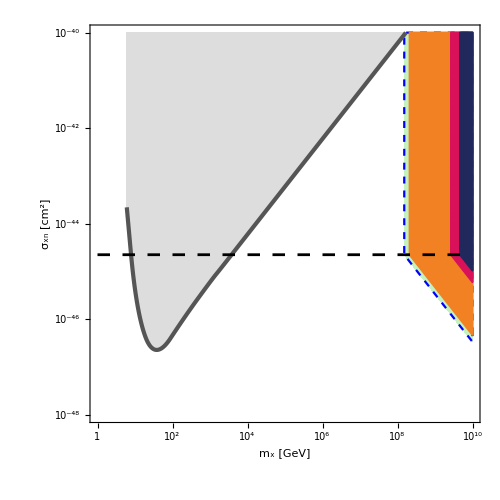

```mathematica
q=Show[RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,2.1*10^6],NchFermion[10^x]]},{x,0,10},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotStyle->RGBColor["#C4F1BE"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,1]≥Max[ Nself[10^x,2.1*10^6],NchFermion[10^x]]},{x,0,10},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#F28123"],BoundaryStyle->RGBColor["#F28123"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.1]≥ Max[ Nself[10^x,2.1*10^6],NchFermion[10^x]]},{x,0,10},{y,-44,-52},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotStyle->RGBColor["#D81159"],BoundaryStyle->RGBColor["#D81159"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],
RegionPlot[{totcapgen[10^x,10^y,0.07]≥ Max[ Nself[10^x,2.1*10^6],NchFermion[10^x]]},{x,0,10},{y,-44,-52},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotPoints->30,PlotStyle->RGBColor["#21295C"],BoundaryStyle->RGBColor["#21295C"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],ListPlot[{Table[{Log10[data1[[i,1]]],-data1[[i,2]]-4},{i,Length[data1]}]},PlotRange->{{0,3},{-44,-64}},PlotStyle->Directive[Darker[Gray],Thickness[0.006]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->450,AspectRatio->1,Joined->True,AxesOrigin->{-2,-36},FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,Filling->Top,FrameTicks->myticks,InterpolationOrder->2],Plot[Log10[sigmasat],{x,0,10},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]]]]//Quiet
```

```mathematica
Export["Collapse_fermion.pdf",q];
```

```mathematica
(*Some useful estimates*)
```

```mathematica
(24^2*π)/(1.57*10^57)
```

1.15258×10^-54

```mathematica
mn=1;
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
```

```mathematica
c=3*10^8;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
g1[600*10^3,100,0.1]
```

0.961266

```mathematica
g1self[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2));
```

```mathematica
g1self[10^6,100,0.01]/g1[10^6,100,0.01]
```

0.0108984

```mathematica
(*************************************************************************************************************************************************************)
```

```mathematica
(*PSR J0437-4715*)(*SELF*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
n=ρ/(1.6725*10^-27);
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
g1self[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2));
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
(*ttherm[mx_?NumericQ,sigma_?NumericQ,T_]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*sigma*kb*T);*)
```

```mathematica
buni[mx_?NumericQ,sigmadmdm_?NumericQ]:=sigmadmdm*ρx/mx*NIntegrate[fMB[u]/u*(vesc^2-u^2),{u,0,vesc}];
duni[mx_?NumericQ,T_?NumericQ]:=π*rth[mx,T]^2*ρx/mx*NIntegrate[fMB[u]/u*(vesc^2-u^2),{u,0,vesc}];
```

```mathematica
bgen[mx_?NumericQ,sigmadmdm_?NumericQ,mphi_?NumericQ]:=sigmadmdm*ρx/mx*NIntegrate[fMB[u]/u*(u^2+vesc^2)*g1self[u,mx,mphi],{u,0,vesc}];

dgen[mx_?NumericQ,T_?NumericQ,mphi_?NumericQ]:=π*rth[mx,T]^2*ρx/mx*NIntegrate[fMB[u]/u*(u^2+vesc^2)*g1self[u,mx,mphi],{u,0,vesc}];
```

```mathematica
tage=6.69*10^9*3.15*10^7;
sigmatherm[mx_?NumericQ,T_?NumericQ]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*tage*kb*T);
```

```mathematica
tsatuni[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ,sigma_?NumericQ]:=1/buni[mx,sigmadmdm]*Log[(auni[mx,sigma]+buni[mx,sigmadmdm]*(π*rth[mx,T]^2)/sigmadmdm)/auni[mx,sigma]];(*estimate of saturation time which is the geometrical limit of self capture*)

 tsatgen[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=

1/bgen[mx,sigmadmdm,mphi]*Log[(agen[mx,sigma,mphi]+bgen[mx,sigmadmdm,mphi]*(π*rth[mx,T]^2)/sigmadmdm)/agen[mx,sigma,mphi]](*estimate of saturation time which is the geometrical limit of self capture*)
```

```mathematica
totcapuni[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ,sigma_?NumericQ]:=If[tsatuni[mx,sigmadmdm,T,sigma]-tage<0,(π*rth[mx,T]^2)/sigmadmdm+(tage-tsatuni[mx,sigmadmdm,T,sigma])*(auni[mx,sigma]+duni[mx,T]),If[buni[mx,sigmadmdm]*tage≥10^-5,auni[mx,sigma]/buni[mx,sigmadmdm]*(Exp[buni[mx,sigmadmdm]*tage]-1),auni[mx,sigma]*(tage+(buni[mx,sigmadmdm]*tage^2)/2)]];
```

```mathematica
totcapgen[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=If[tsatgen[mx,sigmadmdm,T,sigma,mphi]-tage<0,(π*rth[mx,T]^2)/sigmadmdm+(tage-tsatgen[mx,sigmadmdm,T,sigma,mphi])*(agen[mx,sigma,mphi]+dgen[mx,T,mphi]),If[bgen[mx,sigmadmdm,mphi]*tage≥10^-5,agen[mx,sigma,mphi]/bgen[mx,sigmadmdm,mphi]*(Exp[bgen[mx,sigmadmdm,mphi]*tage]-1),agen[mx,sigma,mphi]*(tage+(bgen[mx,sigmadmdm,mphi]*tage^2)/2)]];
```

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27);
```

```mathematica
Mpl=1.2211*10^19;
```

```mathematica
NchBosonself[mx_?NumericQ,λ_?NumericQ]:=2/π*Mpl^2/mx^2*(1+λ/(32*π)*Mpl^2/mx^2)^0.5;
```

```mathematica
myticks2={{{{10^43,"10^43",{0.020,0}},{10^42,"",{0.010,0}},{10^41,"",{0.010,0}},{10^40,"",{0.010,0}},{10^39,"",{0.010,0}},{10^38,"10^38",{0.020,0}},{10^37,"",{0.010,0}},{10^36,"",{0.010,0}},{10^35,"",{0.010,0}},{10^34,"",{0.010,0}},{10^33,"10^33",{0.020,0}},{10^32,"",{0.010,0}},{10^31,"",{0.010,0}},{10^30,"",{0.010,0}},{10^29,"",{0.010,0}},{10^28,"10^28",{0.020,0}},{10^27,"",{0.010,0}},{10^26,"",{0.010,0}},{10^25,"",{0.010,0}},{10^24,"",{0.010,0}},{10^23,"10^23",{0.010,0}}},None},{{{0,"1",{0.020,0}},{Log10[2],"",{0.010,0}},{Log10[3],"",{0.010,0}},{Log10[4],"",{0.010,0}},{Log10[5],"",{0.010,0}},{Log10[6],"",{0.010,0}},{Log10[7],"",{0.010,0}},{Log10[8],"",{0.010,0}},{Log10[9],"",{0.010,0}},{1,"10",{0.020,0}},{Log10[20],"",{0.010,0}},{Log10[30],"",{0.010,0}},{Log10[40],"",{0.010,0}},{Log10[50],"",{0.010,0}},{Log10[60],"",{0.010,0}},{Log10[70],"",{0.010,0}},{Log10[80],"",{0.010,0}},{Log10[90],"",{0.010,0}},{2,"10^2",{0.020,0}},{Log10[200],"",{0.010,0}},{Log10[300],"",{0.010,0}},{Log10[400],"",{0.010,0}},{Log10[500],"",{0.010,0}},{Log10[600],"",{0.010,0}},{Log10[700],"",{0.010,0}},{Log10[800],"",{0.010,0}},{Log10[900],"",{0.010,0}},{3,"10^3",{0.020,0}},{Log10[2000],"",{0.010,0}},{Log10[3000],"",{0.010,0}},{Log10[4000],"",{0.010,0}},{Log10[5000],"",{0.010,0}},{Log10[6000],"",{0.010,0}},{Log10[7000],"",{0.010,0}},{Log10[8000],"",{0.010,0}},{Log10[9000],"",{0.010,0}},{4,"10^4",{0.020,0}},{Log10[2*10^4],"",{0.010,0}},{Log10[3*10^4],"",{0.010,0}},{Log10[4*10^4],"",{0.010,0}},{Log10[5*10^4],"",{0.010,0}},{Log10[6*10^4],"",{0.010,0}},{Log10[7*10^4],"",{0.010,0}},{Log10[8*10^4],"",{0.010,0}},{Log10[9*10^4],"",{0.010,0}},{5,"10^5",{0.020,0}},{Log10[2*10^5],"",{0.010,0}},{Log10[3*10^5],"",{0.010,0}},{Log10[4*10^5],"",{0.010,0}},{Log10[5*10^5],"",{0.010,0}},{Log10[6*10^5],"",{0.010,0}},{Log10[7*10^5],"",{0.010,0}},{Log10[8*10^5],"",{0.010,0}},{Log10[9*10^5],"",{0.010,0}},{6,"10^6",{0.020,0}},{7,"10^7",{0.020,0}},{8,"10^8",{0.020,0}}},None}};
```

```mathematica
(*comp=Show[LogPlot[{auni[10^x,sigmasat]*tage,totcapuni[10^x,10^x/(5.62*10^27),10^5,sigmasat]-auni[10^x,sigmasat]*tage},{x,0,6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotStyle->{Directive[Red,Thickness[0.004]],Directive[Blue,Thickness[0.004]]},FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["Number of captured DM particles",FontSize->20,Bold]},ImageSize->520,AspectRatio->1,PlotLegends->Placed[{Style["Baryonic capture",FontSize->16],Style["Self capture",FontSize->16]},{0.24,0.13}],FrameTicks->myticks2,Epilog->Text[Style["σ_χn = σ_χn^sat",Black,20],Scaled[{.84,.95}]]],Graphics[Rotate[Text[Style["~ 1/m_χ",Darker[Gray],FontSize->16],Scaled[{0.55,0.72}]],0 Degree]],Graphics[Rotate[Text[Style["~ 1/m_χ^2",Darker[Gray],FontSize->16],Scaled[{0.6,0.15}]],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{Scaled[{0.8,0.12}],Scaled[{0.5,0.3}]}]}],Graphics[{Dashed,Darker[Gray],Thick,Line[{Scaled[{0.8,0.7}],Scaled[{0.4,0.82}]}]}]]//Quiet*)
```

```mathematica
comp=Show[LogPlot[{auni[10^x,sigmasat]*tage,totcapuni[10^x,10^x/(5.62*10^27),2.1*10^6,sigmasat]-auni[10^x,sigmasat]*tage},{x,0,6},Frame->True,PlotRange->{{0,6},{10^23,10^43}},FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotStyle->{Directive[Red,Thickness[0.004]],Directive[Blue,Thickness[0.004]]},FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["Number of captured DM particles",FontSize->20,Bold]},ImageSize->520,AspectRatio->1,PlotLegends->Placed[{Style["Baryonic capture",FontSize->16],Style["Self capture",FontSize->16]},{0.24,0.13}],FrameTicks->myticks2,Epilog->Text[Style["σ_χn = σ_χn^sat",Black,20],Scaled[{.84,.95}]]],Graphics[Rotate[Text[Style["~ 1/m_χ",Darker[Gray],FontSize->16],Scaled[{0.55,0.75}]],0 Degree]],Graphics[Rotate[Text[Style["~ 1/m_χ^2",Darker[Gray],FontSize->16],Scaled[{0.6,0.23}]],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{Scaled[{0.8,0.18}],Scaled[{0.5,0.36}]}]}],Graphics[{Dashed,Darker[Gray],Thick,Line[{Scaled[{0.8,0.72}],Scaled[{0.4,0.84}]}]}]]//Quiet
```

-Graphics-

```mathematica
(*comp2=Show[LogPlot[{auni[10^x,(π*rth[10^x,10^5]^2)/Nn]*tage,totcapuni[10^x,10^x/(5.62*10^27),10^5,(π*rth[10^x,10^5]^2)/Nn]-auni[10^x,(π*rth[10^x,10^5]^2)/Nn]*tage},{x,0,6},Frame->True,PlotRange->{{0,6},{10^23,10^38}},FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004]]},FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["Number of captured DM particles",FontSize->20,Bold]},ImageSize->520,AspectRatio->1,PlotLegends->Placed[{Style["Baryonic capture",FontSize->16],Style["Self capture",FontSize->16]},{0.24,0.13}],FrameTicks->myticks2,Epilog->Text[Style["σ_χn = σ_χn^crit",Black,20],Scaled[{.84,.95}]]],Graphics[Rotate[Text[Style["~ 1/m_χ^2",Darker[Gray],FontSize->16],Scaled[{0.6,0.23}]],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{Scaled[{0.8,0.16}],Scaled[{0.5,0.4}]}]}]]//Quiet*)
```

```mathematica
comp2=Show[LogPlot[{auni[10^x,(π*rth[10^x,2.1*10^6]^2)/Nn]*tage,totcapuni[10^x,10^x/(5.62*10^27),2.1*10^6,(π*rth[10^x,2.1*10^6]^2)/Nn]-auni[10^x,(π*rth[10^x,2.1*10^6]^2)/Nn]*tage},{x,0,6},Frame->True,PlotRange->{{0,6},{10^23,10^38}},FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004]]},FrameLabel->{Style["m_χ [GeV]",FontSize->20,Bold],Style["Number of captured DM particles",FontSize->20,Bold]},ImageSize->520,AspectRatio->1,PlotLegends->Placed[{Style["Baryonic capture",FontSize->16],Style["Self capture",FontSize->16]},{0.24,0.13}],FrameTicks->myticks2,Epilog->Text[Style["σ_χn = σ_χn^crit",Black,20],Scaled[{.84,.95}]]],Graphics[Rotate[Text[Style["~ 1/m_χ^2",Darker[Gray],FontSize->16],Scaled[{0.6,0.32}]],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{Scaled[{0.8,0.24}],Scaled[{0.5,0.48}]}]}]]//Quiet
```

-Graphics-

```mathematica
ttherm[mx_?NumericQ,sigma_?NumericQ,T_]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*sigma*kb*T);
```

```mathematica
sigmacrit[mx_?NumericQ,T_]:=10^4*(π*rth[mx,T]^2)/Nn;
```

```mathematica
sigmacrit[100,2.1*10^6]
```

2.49866×10^-53

```mathematica
sigmasat//N
```

2.24834×10^-49

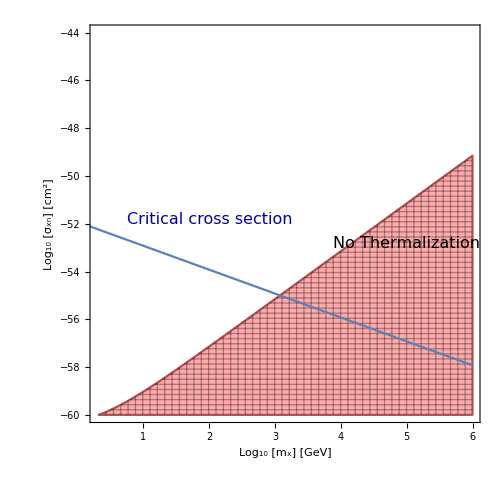

```mathematica
Show[RegionPlot[{ttherm[10^x,10^(y-4),2.1*10^6]≥  tage},{x,Log10[2],6},{y,-44,-60},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Pink],PlotStyle->Lighter[Pink],Mesh->50,FrameLabel->{Style["Log_10 [m_x] [GeV]",FontSize->20,Bold],Style["Log_10 [σ_xn] [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{5,-52.83}],0 Degree]],Plot[Log10[sigmacrit[10^x,10^5]],{x,0,6}],Graphics[Rotate[Text[Style["Critical cross section",Darker[Blue],FontSize->16],{2,-51.83}],0 Degree]]]
```

```mathematica
(*LogPlot[{auni[10^x,10^-52]*tage,totcapuni[10^x,10^x/(5.62*10^27),10^5,10^-52]-auni[10^x,10^-52]*tage},{x,0,6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],PlotRange->{{0,6},{10^23,10^43}},PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.006]]},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["Number of captured DM particles",FontSize->20,Bold]},ImageSize->520,AspectRatio->1,PlotLegends->Placed[{Style["Baryonic capture",FontSize->16],Style["Self capture",FontSize->16]},{0.2,0.2}],FrameTicks->myticks2,Epilog->Text[Style["σ_xn = 10^-48 cm^2",Black,20],Scaled[{.80,.95}]]]//Quiet*)
```

```mathematica
(*ttherm[mx_?NumericQ,sigma_?NumericQ,T_?NumericQ]:=1/(6*2^0.5)*(mx^2*mn)/mr[mx]^3*pf/(n*sigma*kb*T);*)
```

```mathematica
(*Show[RegionPlot[{ttherm[10^x,10^y,10^5]≥  tage},{x,0,6},{y,-44,-60},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Pink],PlotStyle->Lighter[Pink],Mesh->50,FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xn [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{4.2,-57.83}],0 Degree]],Plot[Log10[(π*rth[10^x,10^5]^2)/Nn],{x,0,6},Frame->True]]*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["comparison2.pdf",comp2];
Export["comparison.pdf",comp];
```

```mathematica
totcapuni[10^2,10^2/(5.62*10^27),10^5,10^-51]
```

2.69345×10^38

```mathematica
auni[10^2,10^-51]*tage
```

2.69345×10^38

```mathematica
totcapuni[10^2,10^2/(5.62*10^27),10^5,10^-51]-(auni[10^2,10^-51]*tage)
```

3.20484×10^31

```mathematica
(*LogPlot[{totcapuni[10^x,10^x/(5.62*10^27),2.1*10^6,sigmasat],totcapuni[10^x,10^x/(5.62*10^27),2.1*10^6,10^-52],Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,(64*π*10^x/(5.62*10^27))^0.5*10^x*5.06*10^15]]},{x,0,6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["Log_10 [m_x] [GeV]",FontSize->20,Bold],Style["Number of captured particle",FontSize->20,Bold]},ImageSize->500,AspectRatio->1,PlotLegends->Placed[{"σ_χn= σ_sat","σ_χn= 10^-48 cm^2","Max[N_χ^cha, N_χ^self]"},{0.8,0.8}]]//Quiet*)
```

```mathematica
(*LogPlot[{totcapuni[10^x,10^x/(5.62*10^27),2.1*10^6,sigmasat],totcapuni[10^x,10^x/(5.62*10^27),2.1*10^6,10^-52],Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,0]]},{x,0,6},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["Log_10 [m_x] [GeV]",FontSize->20,Bold],Style["Number of captured particle",FontSize->20,Bold]},ImageSize->500,AspectRatio->1,PlotLegends->Placed[{"σ_χn= σ_sat","σ_χn= 10^-48 cm^2","Max[N_χ^cha, N_χ^self]"},{0.8,0.8}]]//Quiet*)
```

```mathematica
NchBosonself[10^5,10^-90]
```

9.49254×10^27

```mathematica
Nself[10^5,2.1*10^6]
```

1.45373×10^36

```mathematica
(*Hawking Evaporation prevents BH growth*)
```

```mathematica
GN=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
cns=0.17;
```

```mathematica
λ=0.25;
```

```mathematica
mcrit=1/GN*(cns^3/(74*π*4*π*λ*ρ*5.62*10^26*(1.98*10^-16)^3))^0.25;(*critical mass for BH evaporation in GeV*)
```

```mathematica
mcritold=1/GN*(cns^3/(15360*π*4*π*λ*ρ*5.62*10^26*(1.98*10^-16)^3))^0.25;(*critical mass for BH evaporation in GeV*)
```

```mathematica
mcrit
```

2.71619×10^37

```mathematica
Mpl=1.2211*10^19;
```

```mathematica
mcritold
```

7.15601×10^36

```mathematica
myticks={{{{-20,"10^-20",{0.020,0}},{-25,"",{0.010,0}},{-30,"",{0.010,0}},{-35,"",{0.010,0}},{-40,"10^-40",{0.020,0}},{-45,"",{0.010,0}},{-50,"",{0.010,0}},{-55,"",{0.010,0}},{-60,"10^-60",{0.020,0}},{-65,"",{0.010,0}},{-70,"",{0.010,0}},{-75,"",{0.010,0}},{-80,"10^-80",{0.020,0}},{-85,"",{0.010,0}},{-90,"",{0.010,0}},{-95,"",{0.010,0}},{-100,"10^-100",{0.020,0}},{-105,"",{0.010,0}},{-110,"",{0.010,0}}},None},{{{0,"1",{0.020,0}},{Log10[2],"",{0.010,0}},{Log10[3],"",{0.010,0}},{Log10[4],"",{0.010,0}},{Log10[5],"",{0.010,0}},{Log10[6],"",{0.010,0}},{Log10[7],"",{0.010,0}},{Log10[8],"",{0.010,0}},{Log10[9],"",{0.010,0}},{1,"10",{0.020,0}},{Log10[20],"",{0.010,0}},{Log10[30],"",{0.010,0}},{Log10[40],"",{0.010,0}},{Log10[50],"",{0.010,0}},{Log10[60],"",{0.010,0}},{Log10[70],"",{0.010,0}},{Log10[80],"",{0.010,0}},{Log10[90],"",{0.010,0}},{2,"10^2",{0.020,0}},{Log10[200],"",{0.010,0}},{Log10[300],"",{0.010,0}},{Log10[400],"",{0.010,0}},{Log10[500],"",{0.010,0}},{Log10[600],"",{0.010,0}},{Log10[700],"",{0.010,0}},{Log10[800],"",{0.010,0}},{Log10[900],"",{0.010,0}},{3,"10^3",{0.020,0}},{Log10[2000],"",{0.010,0}},{Log10[3000],"",{0.010,0}},{Log10[4000],"",{0.010,0}},{Log10[5000],"",{0.010,0}},{Log10[6000],"",{0.010,0}},{Log10[7000],"",{0.010,0}},{Log10[8000],"",{0.010,0}},{Log10[9000],"",{0.010,0}},{4,"10^4",{0.020,0}},{Log10[2*10^4],"",{0.010,0}},{Log10[3*10^4],"",{0.010,0}},{Log10[4*10^4],"",{0.010,0}},{Log10[5*10^4],"",{0.010,0}},{Log10[6*10^4],"",{0.010,0}},{Log10[7*10^4],"",{0.010,0}},{Log10[8*10^4],"",{0.010,0}},{Log10[9*10^4],"",{0.010,0}},{5,"10^5",{0.020,0}},{Log10[2*10^5],"",{0.010,0}},{Log10[3*10^5],"",{0.010,0}},{Log10[4*10^5],"",{0.010,0}},{Log10[5*10^5],"",{0.010,0}},{Log10[6*10^5],"",{0.010,0}},{Log10[7*10^5],"",{0.010,0}},{Log10[8*10^5],"",{0.010,0}},{Log10[9*10^5],"",{0.010,0}},{6,"10^6",{0.020,0}},{7,"10^7",{0.020,0}},{8,"10^8",{0.020,0}}},None}};
```

```mathematica
(*ps=Show[RegionPlot[{totcapuni[10^x,10^y,2.1*10^6,sigmasat]≥ Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]]},{x,0,6},{y,-20,-110},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,RGBColor["#DB260B"]},PlotStyle->RGBColor["#FBB9AF"],PlotRangePadding->None,ImageSize->520,FrameTicks->myticks],RegionPlot[{totcapuni[10^x,10^y,2.1*10^6,10^-51]≥ Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]]},{x,0,6},{y,-20,-110},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},BoundaryStyle->{Dashed,Blue},PlotStyle->RGBColor["#AAA6DF"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{10^x* NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]<mcrit},{x,0,6},{y,-20,-110},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotStyle->Directive[Gray,Opacity[0.4]],BoundaryStyle->Darker[Gray],PlotRangePadding->None,ImageSize->500],RegionPlot[10^y-1.78*10^-28*10^x>0,{x,-2,6},{y,-20,-110},Frame->True,PlotRangePadding->None,PlotStyle->Directive[Gray,Opacity[0.4]],BoundaryStyle->Darker[Gray]],Graphics[Rotate[Text[Style["Bullet Cluster",Darker[Black],FontSize->14],{2,-28.13}],0 Degree]],Graphics[Rotate[Text[Style["~ m_x^6",Darker[Black],FontSize->16],{4.55,-50.13}],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{4.03,-58.9},{5.63,-49.83}}]}],Graphics[Rotate[Text[Style["Hawking radiation \n prevents BH growth",Darker[Black],FontSize->15],{1.8,-90.23}],0 Degree]],Graphics[Rotate[Text[Style["σ_xn = 2×10^-45 cm^2",RGBColor["#DB260B"],FontSize->16],{2.8,-65.55}],0 Degree]],Graphics[Rotate[Text[Style["σ_xn = 10^-47 cm^2",RGBColor["#3F389C"],FontSize->16],{5.75,-90.23}],90 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{3.8,-65.12},{3.8,-84.95}}]}],Graphics[Rotate[Text[Style["N_self > N_cha",Darker[Black],FontSize->16],{3.15,-72.03}],0 Degree]]]//Quiet*)
```

```mathematica
totcapuni[2*10^5,10^-70,2.1*10^6,10^-51]
```

1.2797×10^35

```mathematica
Max[Nself[2*10^5,2.1*10^6],NchBosonself[2*10^5,(64*π*10^-70)^0.5*2*10^5*5.06*10^15]]
```

2.56985×10^35

```mathematica
(*psv2=Show[RegionPlot[{totcapuni[10^x,10^y,2.1*10^6,sigmasat]≥ Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]]},{x,0,6},{y,-20,-110},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ[GeV]",FontSize->20,Bold],Row[{Style["σ_χχ [",FontSize->20,Bold],Style[Superscript["m","2"],FontSize->20,Bold],Style["]",FontSize->20,Bold]}]},BoundaryStyle->{RGBColor["#DB260B"]},PlotStyle->RGBColor["#FBB9AF"],PlotRangePadding->None,ImageSize->520,FrameTicks->myticks],RegionPlot[{totcapuni[10^x,10^y,2.1*10^6,10^-51]≥ Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]]},{x,0,6},{y,-20,-110},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},BoundaryStyle->{Blue},PlotStyle->RGBColor["#AAA6DF"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{10^x* NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]<mcrit},{x,0,6},{y,-20,-110},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],MeshFunctions->{20*#1-#2&},Mesh->40,MeshStyle->Directive[RGBColor["#3A7D44"],Thickness[0.001]],PlotStyle->Directive[White,Opacity[0.4]],BoundaryStyle->RGBColor["#02B51D"],PlotRangePadding->None,ImageSize->500],RegionPlot[10^y-1.78*10^-28*10^x>0,{x,-2,6},{y,-20,-110},Frame->True,PlotRangePadding->None,PlotStyle->Directive[Gray,Opacity[0.4]],BoundaryStyle->Darker[Gray]],Graphics[Rotate[Text[Style["Bullet Cluster",Darker[Gray],FontSize->16],{2,-23.13}],0 Degree]],Graphics[Rotate[Text[Style["~ m_χ^6",Darker[Gray],FontSize->16],{4.55,-52.53}],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{4.08,-60.31},{5.63,-51.28}}]}],Graphics[Rotate[Text[Style["Efficient DM repulsion",Lighter[Gray],FontSize->16],{1.8,-52.43}],0 Degree]],Graphics[Rotate[Text[Style["DM \n collapse",RGBColor["#ffffff"],FontSize->15],{5,-74.03}],0 Degree]],Graphics[Rotate[Text[Style["Efficient \n Hawking evaporation",RGBColor["#02B51D"],FontSize->16],{2.7,-102.43}],0 Degree]],Graphics[Rotate[Text[Style["σ_χn = σ_χn^sat ",RGBColor["#DB260B"],FontSize->15],{4.2,-74.25}],90 Degree]],Graphics[Rotate[Text[Style["σ_χn = 10^-47 cm^2",RGBColor["#3F389C"],FontSize->15],{5.75,-74.23}],90 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{3.8,-65.12},{3.8,-84.95}}]}],Graphics[Rotate[Text[Style["N_χ^self > N_χ^cha",Darker[Gray],FontSize->16],{3.15,-72.03}],0 Degree]]]//Quiet*)
```

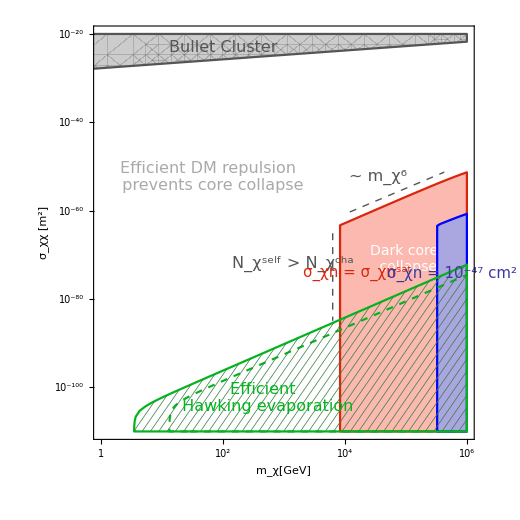

```mathematica
psv2=Show[RegionPlot[{totcapuni[10^x,10^y,2.1*10^6,sigmasat]≥ Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]]},{x,0,6},{y,-20,-110},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ[GeV]",FontSize->20,Bold],Row[{Style["σ_χχ [",FontSize->20,Bold],Style[Superscript["m","2"],FontSize->20,Bold],Style["]",FontSize->20,Bold]}]},BoundaryStyle->{RGBColor["#DB260B"]},PlotStyle->RGBColor["#FBB9AF"],PlotRangePadding->None,ImageSize->520,FrameTicks->myticks],RegionPlot[{totcapuni[10^x,10^y,2.1*10^6,10^-51]≥ Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]]},{x,0,6},{y,-20,-110},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},BoundaryStyle->{Blue},PlotStyle->RGBColor["#AAA6DF"],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],RegionPlot[{10^x* NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]<mcritold},{x,0,6},{y,-20,-110},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotStyle->Transparent,BoundaryStyle->{RGBColor["#02B51D"],Dashed,Thickness[0.003]},PlotRangePadding->None,ImageSize->500],RegionPlot[{10^x* NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]<mcrit},{x,0,6},{y,-20,-110},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],MeshFunctions->{20*#1-#2&},Mesh->40,MeshStyle->Directive[RGBColor["#3A7D44"],Thickness[0.001]],PlotStyle->Transparent,BoundaryStyle->RGBColor["#02B51D"],PlotRangePadding->None,ImageSize->500],RegionPlot[10^y-1.78*10^-28*10^x>0,{x,-2,6},{y,-20,-110},Frame->True,PlotRangePadding->None,PlotStyle->Directive[Gray,Opacity[0.4]],BoundaryStyle->Darker[Gray]],Graphics[Rotate[Text[Style["Bullet Cluster",Darker[Gray],FontSize->16],{2,-23.13}],0 Degree]],Graphics[Rotate[Text[Style["~ m_χ^6",Darker[Gray],FontSize->16],{4.55,-52.53}],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{4.08,-60.31},{5.63,-51.28}}]}],Graphics[Rotate[Text[Style["Efficient DM repulsion \n prevents core collapse",Lighter[Gray],FontSize->16],{1.8,-52.43}],0 Degree]],Graphics[Rotate[Text[Style["Dark core \n collapse",RGBColor["#ffffff"],FontSize->14],{5,-71.03}],0 Degree]],Graphics[Rotate[Text[Style["Efficient \n Hawking evaporation",RGBColor["#02B51D"],FontSize->16],{2.7,-102.43}],0 Degree]],Graphics[Rotate[Text[Style["σ_χn = σ_χn^sat ",RGBColor["#DB260B"],FontSize->15],{4.2,-74.25}],90 Degree]],Graphics[Rotate[Text[Style["σ_χn = 10^-47 cm^2",RGBColor["#3F389C"],FontSize->15],{5.75,-74.23}],90 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{3.8,-65.12},{3.8,-84.95}}]}],Graphics[Rotate[Text[Style["N_χ^self > N_χ^cha",Darker[Gray],FontSize->16],{3.15,-72.03}],0 Degree]]]//Quiet
```

```mathematica
(*p=ContourPlot[{totcapuni[10^x,10^y,2.1*10^6,sigmasat]== Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]]},{x,0,6},{y,-20,-110},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]]]//Quiet*)
```

$Aborted

```mathematica
(*q=ContourPlot[{totcapuni[10^x,10^y,2.1*10^6,10^-51]== Max[Nself[10^x,2.1*10^6],NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]]},{x,0,6},{y,-20,-110},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]]]//Quiet*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
pp=Import["data1.txt","Table"];
qq=Import["data2.txt","Table"];
```

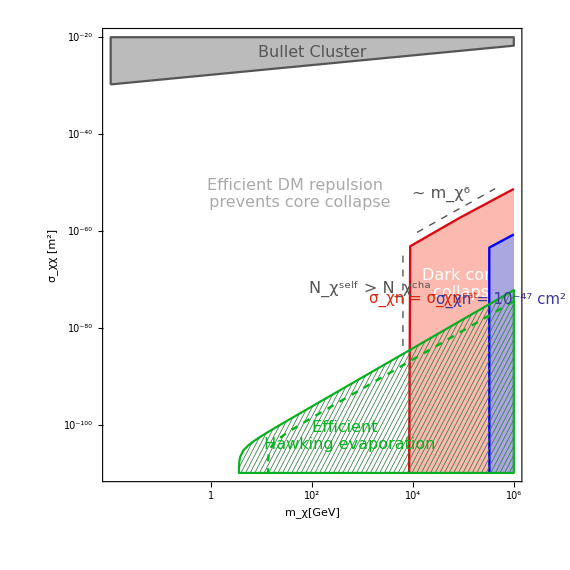

```mathematica
a=Show[ListPlot[{Table[{pp[[i,1]],pp[[i,2]]},{i,Length[pp]}]},PlotRange->{{0,6},{-20,-110}},Frame->True,PlotStyle->Directive[RGBColor["#DB0B13"],Thickness[0.003]],FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->570,AspectRatio->1,Joined->True,FillingStyle->RGBColor["#FBB9AF"],FrameLabel->{Style["m_χ[GeV]",FontSize->22],Row[{Style["σ_χχ [",FontSize->22],Style[Superscript["m","2"],FontSize->22],Style["]",FontSize->22]}]},
PlotRangePadding->None,Filling->Bottom,InterpolationOrder->1,FrameTicks->myticks],

ListPlot[{Table[{qq[[i,1]],qq[[i,2]]},{i,Length[qq]}]},PlotRange->{{0,6},{-20,-110}},Frame->True,PlotStyle->Directive[Blue,Thickness[0.003]],FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,Joined->True,FillingStyle->RGBColor["#AAA6DF"],FrameLabel->{Style["m_χ[GeV]",FontSize->22],Row[{Style["σ_χχ [",FontSize->22],Style[Superscript["m","2"],FontSize->22],Style["]",FontSize->22]}]},
PlotRangePadding->None,Filling->Bottom,InterpolationOrder->1,FrameTicks->myticks],

RegionPlot[{10^x* NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]<mcrit},{x,0,6},{y,-20,-110},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],MeshFunctions->{20*#1-#2&},Mesh->60,MeshStyle->Directive[RGBColor["#3A7D44"],Thickness[0.001]],PlotStyle->Transparent,BoundaryStyle->RGBColor["#02B51D"],PlotRangePadding->None,ImageSize->500],

ContourPlot[{10^x* NchBosonself[10^x,(64*π*10^y)^0.5*10^x*5.06*10^15]==mcritold},{x,0,6},{y,-20,-110},Frame->True,PlotPoints->100,ContourStyle->{RGBColor["#02B51D"],Dashed,Thickness[0.003]},FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],PlotRangePadding->None,ImageSize->500],



RegionPlot[10^y-1.78*10^-28*10^x>0,{x,-2,6},{y,-20,-110},Frame->True,PlotRangePadding->None,PlotStyle->Directive[RGBColor["#bbbbbb"]],BoundaryStyle->Darker[Gray]],

Graphics[Rotate[Text[Style["Bullet Cluster",Darker[Gray],FontSize->16],{2,-23.13}],0 Degree]],Graphics[Rotate[Text[Style["~ m_χ^6",Darker[Gray],FontSize->16],{4.55,-52.53}],0 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{4.08,-60.31},{5.63,-51.28}}]}],Graphics[Rotate[Text[Style["Efficient DM repulsion \n prevents core collapse",Lighter[Gray],FontSize->16],{1.7,-52.43}],0 Degree]],Graphics[Rotate[Text[Style["Dark core \n collapse",RGBColor["#ffffff"],FontSize->16],{5,-71.03}],0 Degree]],Graphics[Rotate[Text[Style["Efficient \n Hawking evaporation",RGBColor["#02B51D"],FontSize->16],{2.7,-102.43}],0 Degree]],Graphics[Rotate[Text[Style["σ_χn = σ_χn^sat ",RGBColor["#DB260B"],FontSize->15],{4.2,-74.25}],90 Degree]],Graphics[Rotate[Text[Style["σ_χn = 10^-47 cm^2",RGBColor["#3F389C"],FontSize->15],{5.75,-74.23}],90 Degree]],Graphics[{Dashed,Darker[Gray],Thick,Line[{{3.8,-65.12},{3.8,-84.15}}]}],Graphics[Rotate[Text[Style["N_χ^self > N_χ^cha",Darker[Gray],FontSize->16],{3.15,-72.03}],0 Degree]]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Export["DMself.pdf",psv2];*)
Export["DMself.pdf",a];
```